# Just launch the code below to run the notebook (shift+enter)

```mathematica
ClearAll["Global`*"]
BlockEvaluation[tag_]:=Block[{},
nb=EvaluationNotebook[];
NotebookFind[nb,tag,All,CellTags];
SelectionEvaluate[nb]
]
dropdownDialog[list_,phrase_]:=DialogInput[{choice=""},Column[{TextCell[phrase],PopupMenu[Dynamic[choice],list],Button["OK",DialogReturn[choice]]}]]
infoDialog[phrase_]:=DialogInput[{choice=""},Column[{TextCell[phrase],Button["Proceed",DialogReturn[choice]]}]]
If[(DirectoryQ[FileNameJoin[{NotebookDirectory[],"Auxiliary data"}]]//ToString)=="False",CreateDirectory[FileNameJoin[{NotebookDirectory[],"Auxiliary data"}]]];
If[(DirectoryQ[FileNameJoin[{NotebookDirectory[],"Auxiliary data/HNLs"}]]//ToString)=="False",CreateDirectory[FileNameJoin[{NotebookDirectory[],"Auxiliary data/HNLs"}]]];
tagslist={"Evaluation","Evaluation-sensitivity"};
choiceslist={"Tabulated number of events+sensitivity","Sensitivity only"};
computationchoice=dropdownDialog[choiceslist,"Do you want to compute the tabulated number of events and then sensitivity, or just sensitivity (if the tabulate number of events has been already produced)?"];
tagselected=If[computationchoice=="Tabulated number of events+sensitivity","Evaluation","Evaluation-sensitivity"];
BlockEvaluation[tagselected]
```

# Preliminary definitions (launch first)

## Parameters and various functions

```mathematica
dropdownDialog[list_,phrase_]:=DialogInput[{choice=""},Column[{TextCell[phrase],PopupMenu[Dynamic[choice],list],Button["OK",DialogReturn[choice]]}]]
infoDialog[phrase_]:=DialogInput[{choice=""},Column[{TextCell[phrase],Button["Proceed",DialogReturn[choice]]}]]
(*chbar*)
chbar= 6.6*10^-25*3*10^8;
(*Masses of various SM particles*)
mB=5.3;
mBc=6.3;
mK=0.495;
mDs=1.97;
mD=1.87;
MZ=91;
MW=80;
MπCh= 0.13957;
Mπ0=0.134977;
MK=0.493677;
Mρ = 0.77549;
Mη = 0.547853;
Mηprime = 0.95766;
Mηc=2.9803;
Mω=0.78265;
Mϕ=1.019455;
MD=1.86484;
MDs=1.9685;
MDsStar=2.1123;
MJψ=3.097;
Me = 0.00051099891;
Mμ =0.105658 ;
Mτ = 1.77684;
Ml={Me,Mμ,Mτ};
Mu = {0.0024,1.27,173};
Md = {0.0048,0.104,5};
(*Fermi coupling*)
Gf=1.166379*10^-5;
(*Meson couplings*)
fπ = 0.13;
fK=0.1556;
fη = 0.0817;
fηprime = 0.094;
fηc=0.237;
fD=0.212;
fDs=0.249;
fDsStar=0.315;
gω=0.153;
gϕ=0.234;
gρ = 0.162;
gJψ=1.29;
(*Decay widths of particles at rest in GeV*)
GammatotalZ=2.49;
GammatotalW=2.085;
ΔΓZmax=0.0023;
GammaDs = 1.33*10^-12;
(*τ lepton lifetime*)
ττ = 290.3*10^-15;
(*CKM matrix*)
CKM1 = {{0.9743, 0.2251,0.00351},{0.2249,0.9730,0.0412},{0.00867,0.0404,0.999}};
(*sin^2(Subscript[θ, W])*)
sw2 = 0.23126;
(*Br of decay of η^0 and η' mesons to charged states*)
Bretatocharged=0.28;
Bretaprimetocharged=0.78;
(*Br of decay of ω^0 and ϕ^0 mesons to charged states*)
Brphitocharged=0.66;
Bromegatocharged=0.91;
(*Fragmentation fractions at the LHC*)
fdstau = 0.0543;
fctod0LHC=0.553;
fctodplusLHC = 0.225;
fctodsLHC=0.105;
fbtobcLHC= 2.6*10^-3;
fbtob0LHC=fbtobplusLHC=0.324;
```

## Branching ratios of the HNL production

## ∑_meson f_(q→meson)*Br(meson→N) at U^2 = 1

### 1. LHC

```mathematica
dNeLHC[mN_]=Interpolation[Import[FileNameJoin@Append[FileNameSplit@NotebookDirectory[],"phenomenology/HNL/branching ratios/c_quark_to_N_mixing_e_LHC.dat"],"Table"],InterpolationOrder->1][mN];
dNμLHC[mN_]=Interpolation[Import[FileNameJoin@Append[FileNameSplit@NotebookDirectory[],"phenomenology/HNL/branching ratios/c_quark_to_N_mixing_mu_LHC.dat"],"Table"],InterpolationOrder->1][mN];
dNτLHC[mN_]=Interpolation[Import[FileNameJoin@Append[FileNameSplit@NotebookDirectory[],"phenomenology/HNL/branching ratios/c_quark_to_N_mixing_tau_LHC.dat"],"Table"],InterpolationOrder->1][mN];
bNeLHC[mN_]=Interpolation[Import[FileNameJoin@Append[FileNameSplit@NotebookDirectory[],"phenomenology/HNL/branching ratios/b_quark_to_N_mixing_e_LHC.dat"],"Table"],InterpolationOrder->1][mN];bNμLHC[mN_]=If[mN<6.279-0.105,Evaluate[Interpolation[Import[FileNameJoin@Append[FileNameSplit@NotebookDirectory[],"phenomenology/HNL/branching ratios/b_quark_to_N_mixing_mu_LHC.dat"],"Table"],InterpolationOrder->1][mN]],0];bNτLHC[mN_]=Interpolation[Import[FileNameJoin@Append[FileNameSplit@NotebookDirectory[],"phenomenology/HNL/branching ratios/b_quark_to_N_mixing_tau_LHC.dat"],"Table"],InterpolationOrder->1][mN];
```

### 2. SPS

```mathematica
dNeSPS[mN_]=Interpolation[Import[FileNameJoin@Append[FileNameSplit@NotebookDirectory[],"phenomenology/HNL/branching ratios/c_quark_to_N_mixing_e_SPS.dat"],"Table"],InterpolationOrder->1][mN];
dNμSPS[mN_]=Interpolation[Import[FileNameJoin@Append[FileNameSplit@NotebookDirectory[],"phenomenology/HNL/branching ratios/c_quark_to_N_mixing_mu_SPS.dat"],"Table"],InterpolationOrder->1][mN];
dNτSPS[mN_]=Interpolation[Import[FileNameJoin@Append[FileNameSplit@NotebookDirectory[],"phenomenology/HNL/branching ratios/c_quark_to_N_mixing_tau_SPS.dat"],"Table"],InterpolationOrder->1][mN];
bNeSPS[mN_]=Interpolation[Import[FileNameJoin@Append[FileNameSplit@NotebookDirectory[],"phenomenology/HNL/branching ratios/b_quark_noBc_to_N_mixing_e_SPS.dat"],"Table"],InterpolationOrder->1][mN];bNμSPS[mN_]=If[mN<5.279-0.105,Evaluate[Interpolation[Import[FileNameJoin@Append[FileNameSplit@NotebookDirectory[],"phenomenology/HNL/branching ratios/b_quark_noBc_to_N_mixing_mu_SPS.dat"],"Table"],InterpolationOrder->1][mN]],0];bNτSPS[mN_]=Interpolation[Import[FileNameJoin@Append[FileNameSplit@NotebookDirectory[],"phenomenology/HNL/branching ratios/b_quark_noBc_to_N_mixing_tau_SPS.dat"],"Table"],InterpolationOrder->1][mN];
```

### 3. FermilabBD/DUNE (120 GeV beam)

```mathematica
dNeFermilabBD[mN_]=Interpolation[Import[FileNameJoin@Append[FileNameSplit@NotebookDirectory[],"phenomenology/HNL/branching ratios/c_quark_to_N_mixing_e_FermilabBD.dat"],"Table"],InterpolationOrder->1][mN];
dNμFermilabBD[mN_]=Interpolation[Import[FileNameJoin@Append[FileNameSplit@NotebookDirectory[],"phenomenology/HNL/branching ratios/c_quark_to_N_mixing_mu_FermilabBD.dat"],"Table"],InterpolationOrder->1][mN];
dNτFermilabBD[mN_]=Interpolation[Import[FileNameJoin@Append[FileNameSplit@NotebookDirectory[],"phenomenology/HNL/branching ratios/c_quark_to_N_mixing_tau_FermilabBD.dat"],"Table"],InterpolationOrder->1][mN];
bNeFermilabBD[mN_]=Interpolation[Import[FileNameJoin@Append[FileNameSplit@NotebookDirectory[],"phenomenology/HNL/branching ratios/b_quark_noBc_to_N_mixing_e_FermilabBD.dat"],"Table"],InterpolationOrder->1][mN];
bNμFermilabBD[mN_]=Interpolation[Import[FileNameJoin@Append[FileNameSplit@NotebookDirectory[],"phenomenology/HNL/branching ratios/b_quark_noBc_to_N_mixing_mu_FermilabBD.dat"],"Table"],InterpolationOrder->1][mN];
bNτFermilabBD[mN_]=Interpolation[Import[FileNameJoin@Append[FileNameSplit@NotebookDirectory[],"phenomenology/HNL/branching ratios/b_quark_noBc_to_N_mixing_tau_FermilabBD.dat"],"Table"],InterpolationOrder->1][mN];
```

### 4. FCC-hh

```mathematica
(*For the moment, LHC values are used*)
dNeFCChh[mN_]=Interpolation[Import[FileNameJoin@Append[FileNameSplit@NotebookDirectory[],"phenomenology/HNL/branching ratios/c_quark_to_N_mixing_e_LHC.dat"],"Table"],InterpolationOrder->1][mN];
dNμFCChh[mN_]=Interpolation[Import[FileNameJoin@Append[FileNameSplit@NotebookDirectory[],"phenomenology/HNL/branching ratios/c_quark_to_N_mixing_mu_LHC.dat"],"Table"],InterpolationOrder->1][mN];
dNτFCChh[mN_]=Interpolation[Import[FileNameJoin@Append[FileNameSplit@NotebookDirectory[],"phenomenology/HNL/branching ratios/c_quark_to_N_mixing_tau_LHC.dat"],"Table"],InterpolationOrder->1][mN];
bNeFCChh[mN_]=Interpolation[Import[FileNameJoin@Append[FileNameSplit@NotebookDirectory[],"phenomenology/HNL/branching ratios/b_quark_to_N_mixing_e_LHC.dat"],"Table"],InterpolationOrder->1][mN];bNμFCChh[mN_]=Interpolation[Import[FileNameJoin@Append[FileNameSplit@NotebookDirectory[],"phenomenology/HNL/branching ratios/b_quark_to_N_mixing_mu_LHC.dat"],"Table"],InterpolationOrder->1][mN];bNτFCChh[mN_]=Interpolation[Import[FileNameJoin@Append[FileNameSplit@NotebookDirectory[],"phenomenology/HNL/branching ratios/b_quark_to_N_mixing_tau_LHC.dat"],"Table"],InterpolationOrder->1][mN];
```

## Production W→ N+l

### Mixing case

```mathematica
(*Import["https://raw.githubusercontent.com/FeynCalc/feyncalc/master/install.m"]
InstallFeynCalc[]*)
(*SetDirectory["/Users/miksi/AppData/Roaming/Mathematica/Applications/FeynCalc"];*)
<<FeynCalc`
M=g/(2*Sqrt[2])SpinorUBar[k1,ml].GA[μ].(1-GA5).SpinorV[k2,mN]*PolarizationVector[p,μ];
Mstar = ComplexConjugate[M]/.{μ->μC}
Msquared=Simplify[Expand[1/3 DoPolarizationSums[FermionSpinSum[M Mstar]/.DiracTrace->TR//Contract//Simplify,p]]/.{ScalarProduct[p,p]->mW^2,ScalarProduct[k1,k1]-> ml^2,ScalarProduct[k1,p]-> (mW^2+ml^2-mN^2)/2,ScalarProduct[k2,p]-> (mN^2+mW^2-ml^2)/2,ScalarProduct[k1,k2]->(mW^2-mN^2-ml^2)/2}];
(*Solution of the HNL momentum in rest frame of the W boson*)
PN[mN_,mW_,ml_]=p/.Solve[mW==Sqrt[p^2+mN^2]+Sqrt[p^2+ml^2],p][[2]];
(*Total Br of the process W -> l + N*)
TotalBrWtoN[mN_,mW_,ml_,U2_]=U2/GammatotalW 1/(8*Pi)Msquared*PN[mN,mW,ml]/mW^2/.{g^2->4*Sqrt[2]Gf*mW^2};
Print["Checking the correctness of the calculations - evaluation of total Br of decay at zero HNL mass for mixing with electron (should be 0.108, from pdg):"]
TotalBrWtoN[0,MW,0,1]
```

FeynCalc is already loaded! If you are trying to reload FeynCalc or load FeynArts, TARCER, PHI, FeynHelpers or any other add-on, please restart the kernel.

$Aborted

(g ((ε̄)^*)^($AL($849))(p) (φ(-OverBar[k2],mN)).((γ̄)^5+1).(γ̄)^($AL($849)).(φ(OverBar[k1],ml)))/(2 √2)

Solve::nongen: There may be values of the parameters for which some or all solutions are not valid.

Checking the correctness of the calculations - evaluation of total Br of decay at zero HNL mass for mixing with electron (should be 0.108, from pdg):

0.107445

## Production Z → N+ν

```mathematica
(*Import["https://raw.githubusercontent.com/FeynCalc/feyncalc/master/install.m"]
InstallFeynCalc[]*)
(*SetDirectory["/Users/miksi/AppData/Roaming/Mathematica/Applications/FeynCalc"];*)
<<FeynCalc`
MZdecayMixing=(g/(4*cosθW))SpinorUBar[k1,0].GA[μ].(1-GA5).SpinorV[k2,mN]*PolarizationVector[p,μ];
MZdecayMixingStar = ComplexConjugate[MZdecayMixing]/.{μ->μC}
MZdecayMixingSquared=(1/3 DoPolarizationSums[FermionSpinSum[MZdecayMixing MZdecayMixingStar]/.DiracTrace->TR//Contract//Simplify,p]//Expand)/.{ScalarProduct[p,p]->mZ^2,ScalarProduct[k1,k1]-> 0,ScalarProduct[k1,p]-> (mZ^2-mN^2)/2,ScalarProduct[k2,p]-> (mN^2+mZ^2)/2,ScalarProduct[k1,k2]->(mZ^2-mN^2)/2}//Simplify;
(*HNL momentum in rest frame of the Z boson*)
PNZdecayMixing[mN_,mZ_]=p/.Solve[mZ==Sqrt[p^2+mN^2]+p,p][[1]];
(*Total Br*)
TotalBrZtoNe[mN_,mZ_,U2_]=U2/GammatotalZ 1/(8*Pi)MZdecayMixingSquared*PNZdecayMixing[mN,mZ]/mZ^2/.{g^2->4*Sqrt[2]Gf*(mZ^2 cosθW^2)};
Print["Checking the correctness of the calculations - evaluation of total Br of decay at zero HNL mass for mixing with electron (should be 0.06, from pdg):"]
TotalBrZtoNe[0,MZ,1]
```

FeynCalc is already loaded! If you are trying to reload FeynCalc or load FeynArts, TARCER, PHI, FeynHelpers or any other add-on, please restart the kernel.

$Aborted

(g ((ε̄)^*)^($AL($860))(p) (φ(-OverBar[k2],mN)).((γ̄)^5+1).(γ̄)^($AL($860)).(φ(OverBar[k1])))/(4 cosθW)

Solve::nongen: There may be values of the parameters for which some or all solutions are not valid.

Checking the correctness of the calculations - evaluation of total Br of decay at zero HNL mass for mixing with electron (should be 0.06, from pdg):

0.0662092

## Common function

```mathematica
(*At U^2 = 1*)
χMotherToN[mN_,mixing_,mother_,facility_]:=Association[{{mN,"e","D","SPS"}->dNeSPS[mN],{mN,"e","B","SPS"}->bNeSPS[mN],{mN,"e","W","SPS"}->0,{mN,"e","D","LHC"}->dNeLHC[mN],{mN,"e","B","LHC"}->bNeLHC[mN],{mN,"e","W","LHC"}->TotalBrWtoN[mN,MW,Me,1],{mN,"e","D","FCC-hh"}->dNeFCChh[mN],{mN,"e","B","FCC-hh"}->bNeFCChh[mN],{mN,"e","W","FCC-hh"}->TotalBrWtoN[mN,MW,Me,1],{mN,"e","D","FermilabBD"}->dNeFermilabBD[mN],{mN,"e","B","FermilabBD"}->bNeFermilabBD[mN],{mN,"e","W","FermilabBD"}->0,{mN,"μ","D","SPS"}->dNμSPS[mN],{mN,"μ","B","SPS"}->bNμSPS[mN],{mN,"μ","W","SPS"}->0,{mN,"μ","D","LHC"}->dNμLHC[mN],{mN,"μ","B","LHC"}->bNμLHC[mN],{mN,"μ","W","LHC"}->If[mN<MW-Mμ,Evaluate[TotalBrWtoN[mN,MW,Mμ,1],0]],{mN,"μ","D","FCC-hh"}->dNμFCChh[mN],{mN,"μ","B","FCC-hh"}->bNμFCChh[mN],{mN,"μ","W","FCC-hh"}->If[mN<MW-Mμ,TotalBrWtoN[mN,MW,Mμ,1],0],{mN,"μ","D","FermilabBD"}->dNeFermilabBD[mN],{mN,"μ","B","FermilabBD"}->bNμFermilabBD[mN],{mN,"μ","W","FermilabBD"}->0,{mN,"τ","D","SPS"}->dNτSPS[mN],{mN,"τ","B","SPS"}->bNτSPS[mN],{mN,"τ","W","SPS"}->0,{mN,"τ","D","LHC"}->dNτLHC[mN],{mN,"τ","B","LHC"}->bNτLHC[mN],{mN,"τ","W","LHC"}->If[mN<MW-Mτ,Evaluate[TotalBrWtoN[mN,MW,Mτ,1]],0],{mN,"τ","D","FCC-hh"}->dNτFCChh[mN],{mN,"τ","B","FCC-hh"}->bNτFCChh[mN],{mN,"τ","W","FCC-hh"}->If[mN<MW-Mτ,Evaluate[TotalBrWtoN[mN,MW,Mτ,1]],0],{mN,"τ","D","FermilabBD"}->dNτFermilabBD[mN],{mN,"τ","B","FermilabBD"}->bNτFermilabBD[mN],{mN,"τ","W","FermilabBD"}->0}][{mN,mixing,mother,facility}]
```

## HNL decay width, Br_vis, and decay length

```mathematica
TableGtote=Import[FileNameJoin[{NotebookDirectory[],"phenomenology/HNL/decay widths/decay-width-Ue.dat"}],"Data"];
TableGtotμ=Import[FileNameJoin[{NotebookDirectory[],"phenomenology/HNL/decay widths/decay-width-Umu.txt"}],"Table"];
TableGtotτ=Import[FileNameJoin[{NotebookDirectory[],"phenomenology/HNL/decay widths/decay-width-Utau.txt"}],"Table"];
Γtote[mN_,U2_]=Quiet[10^(Interpolation[{Log10[#[[1]]],Log10[#[[2]]]}&/@TableGtote][Log10[mN]])*U2];
Γtotμ[mN_,U2_]=Quiet[10^(Interpolation[{Log10[#[[1]]],Log10[#[[2]]]}&/@TableGtotμ][Log10[mN]])*U2];
Γtotτ[mN_,U2_]=Quiet[10^(Interpolation[{Log10[#[[1]]],Log10[#[[2]]]}&/@TableGtotτ][Log10[mN]])*U2];
(*Br ratio of visible decays. Two types: when decays into neutral mesons decaying into photons are not included (if the given experiment does not have a ECAL), and when included*)
TableBrVis=Import[FileNameJoin[{NotebookDirectory[],"phenomenology/HNL/decay widths/BrVis.dat"}],"Table"];
BrevisibleCharged[mN_]=Quiet[Interpolation[TableBrVis[[All,{1,2}]],InterpolationOrder->1][mN]];
BrμvisibleCharged[mN_]=Quiet[Interpolation[TableBrVis[[All,{1,3}]],InterpolationOrder->1][mN]];
BrτvisibleCharged[mN_]=Quiet[Interpolation[TableBrVis[[All,{1,4}]],InterpolationOrder->1][mN]];
BrevisibleChargedAndPhotons[mN_]=Quiet[Interpolation[TableBrVis[[All,{1,5}]],InterpolationOrder->1][mN]];
BrμvisibleChargedAndPhotons[mN_]=Quiet[Interpolation[TableBrVis[[All,{1,6}]],InterpolationOrder->1][mN]];
BrτvisibleChargedAndPhotons[mN_]=Quiet[Interpolation[TableBrVis[[All,{1,7}]],InterpolationOrder->1][mN]];
BrVisMixing[mN_,mixing_,ECAL_]:=Association[{{mN,"e","False"}-> BrevisibleCharged[mN],{mN,"μ","False"}->  BrμvisibleCharged[mN],{mN,"τ","False"}-> BrτvisibleCharged[mN],{mN,"e","True"}-> BrevisibleChargedAndPhotons[mN],{mN,"μ","True"}->  BrμvisibleChargedAndPhotons[mN],{mN,"τ","True"}-> BrτvisibleChargedAndPhotons[mN]}][{mN,mixing,ECAL}]
```

## Compilable interpolation function mapping one grid into another

### 3D to 3D

```mathematica
nd=3;
cf3=Module[{xgvars=Unique["xg"]&/@slist@@Range@nd,igvars=Unique["ig"]&/@slist@@Range@nd,tgvars=Unique["tg"]&/@slist@@Range@nd,ivars=Unique["i"]&/@slist@@Range@nd,svars=Unique["s"]&/@slist@@Range@nd,tvars=Unique["t"]&/@slist@@Range@nd,jvars=Unique["j"]&/@slist@@Range@nd},Inactivate[Compile[{seq@{xgvars,_Real,1},{y,_Real,nd}},Module[{seq@igvars,seq@tgvars,seq@ivars,seq@svars,seq@tvars},seq[igvars=Floor[xgvars]-UnitStep[xgvars-indexed@Dimensions@y]];
seq[tgvars=xgvars-igvars];
Table[seq[tvars=Compile`GetElement[tgvars,jvars]];
seq[ivars=Compile`GetElement[igvars,jvars]];
seq[svars=1.-tvars];
eval@Total[Times@@#[[All,1]] Compile`GetElement[y,Sequence@@#[[All,2]]]&/@Tuples@Transpose[{{svars,ivars},{tvars,ivars+1}},{2,3,1}]],seq@{jvars,Length@igvars}]],CompilationTarget->"C",RuntimeAttributes->{Listable},Parallelization->True,RuntimeOptions->"Speed"],Except[seq|eval|indexed]]/.seq[expr_]:>RuleCondition@(Sequence@@Table[Inactivate[expr,Except[slist|indexed]]/.{l_slist:>l[[i]],indexed[l_]:>Inactive[Compile`GetElement][l,i]},{i,nd}])/.eval@expr_:>RuleCondition[Activate[expr/.slist->List]]]//Activate;
```

### 4D to 4D

```mathematica
nd=4;
cf4=Module[{xgvars=Unique["xg"]&/@slist@@Range@nd,igvars=Unique["ig"]&/@slist@@Range@nd,tgvars=Unique["tg"]&/@slist@@Range@nd,ivars=Unique["i"]&/@slist@@Range@nd,svars=Unique["s"]&/@slist@@Range@nd,tvars=Unique["t"]&/@slist@@Range@nd,jvars=Unique["j"]&/@slist@@Range@nd},Inactivate[Compile[{seq@{xgvars,_Real,1},{y,_Real,nd}},Module[{seq@igvars,seq@tgvars,seq@ivars,seq@svars,seq@tvars},seq[igvars=Floor[xgvars]-UnitStep[xgvars-indexed@Dimensions@y]];
seq[tgvars=xgvars-igvars];
Table[seq[tvars=Compile`GetElement[tgvars,jvars]];
seq[ivars=Compile`GetElement[igvars,jvars]];
seq[svars=1.-tvars];
eval@Total[Times@@#[[All,1]] Compile`GetElement[y,Sequence@@#[[All,2]]]&/@Tuples@Transpose[{{svars,ivars},{tvars,ivars+1}},{2,3,1}]],seq@{jvars,Length@igvars}]],CompilationTarget->"C",RuntimeAttributes->{Listable},Parallelization->True,RuntimeOptions->"Speed"],Except[seq|eval|indexed]]/.seq[expr_]:>RuleCondition@(Sequence@@Table[Inactivate[expr,Except[slist|indexed]]/.{l_slist:>l[[i]],indexed[l_]:>Inactive[Compile`GetElement][l,i]},{i,nd}])/.eval@expr_:>RuleCondition[Activate[expr/.slist->List]]]//Activate;
```

# Specifying the experiment and HNL

```mathematica
SetDirectory[NotebookDirectory[]];
(*Parent directory*)
NotebookDirectory[]//ParentDirectory;
AcceptanceDirectory=FileNameJoin[{NotebookDirectory[],"Acceptances"}];
ExperimentDirectoriesList=Select[FileNames["*",AcceptanceDirectory,1],DirectoryQ];
(*List of available experiments (for which the geometry has been implemented)*)
ExperimentsListTemp=Table[FileNameTake[ExperimentDirectoriesList[[i]],-1],{i,1,Length[ExperimentDirectoriesList],1}];
ExperimentsListTemp2=Join[Partition[ExperimentsListTemp,1],Table[{TrueQ@FileExistsQ@FileNameJoin[{NotebookDirectory[],"Acceptances",ExperimentsListTemp[[i]],ToString@StringForm["Acceptance_``_for_HNL-mixing-e.m",ExperimentsListTemp[[i]]]}]},{i,1,Length[ExperimentsListTemp]}],2];
ExperimentsListTemp3=Join[ExperimentsListTemp2[[All,{1}]],Table[{TrueQ@FileExistsQ@FileNameJoin[{NotebookDirectory[],"Acceptances",ExperimentsListTemp2[[i]][[1]],ToString@StringForm["Acceptance_``_for_HNL-mixing-μ.m",ExperimentsListTemp2[[i]][[1]]]}]},{i,1,Length[ExperimentsListTemp2]}],2];
ExperimentsListTemp4=Join[ExperimentsListTemp3[[All,{1}]],Table[{TrueQ@FileExistsQ@FileNameJoin[{NotebookDirectory[],"Acceptances",ExperimentsListTemp3[[i]][[1]],ToString@StringForm["Acceptance_``_for_HNL-mixing-τ.m",ExperimentsListTemp3[[i]][[1]]]}]},{i,1,Length[ExperimentsListTemp3]}],2];
ExperimentsList=Select[ExperimentsListTemp4,#[[2]]==True&][[All,1]]//Sort
If[Length[ExperimentsList]==0,Print["No experiment is available, generate first the acceptance for the given experiment using module 1"]]
Print["Selected experiment:"]
dropdownDialog[list_,phrase_]:=DialogInput[{choice=""},Column[{TextCell[phrase],PopupMenu[Dynamic[choice],list],Button["OK",DialogReturn[choice]]}]]
SelectedExperiment=If[Length[ExperimentsList]≠0,dropdownDialog[ExperimentsList,"Select the experiment:"]]
ListHNLtype={"Dirac","Majorana"};
HNLtype=dropdownDialog[ListHNLtype,"Select the HNL type:"];
Print["HNL type:"]
HNLtype
MixingPatterne=DialogInput[{pattern=""},Column[{"Enter the mixing pattern (U^2)_e:(U^2)_μ:(U^2)_τ = U^2(x_e:x_μ:x_τ). x_e = ",InputField[Dynamic[pattern],Number],Button["Proceed",DialogReturn[pattern],ImageSize->Automatic]}]];
MixingPatternμ=DialogInput[{pattern=""},Column[{"Enter the mixing pattern (U^2)_e:(U^2)_μ:(U^2)_τ = U^2(x_e:x_μ:x_τ). x_μ = ",InputField[Dynamic[pattern],Number],Button["Proceed",DialogReturn[pattern],ImageSize->Automatic]}]];
MixingPatternτ=DialogInput[{pattern=""},Column[{"Enter the mixing pattern (U^2)_e:(U^2)_μ:(U^2)_τ = U^2(x_e:x_μ:x_τ). x_τ = ",InputField[Dynamic[pattern],Number],Button["Proceed",DialogReturn[pattern],ImageSize->Automatic]}]];
Print["Mixing pattern:"]
MixingPattern=(MixingPatterne+MixingPatternμ+MixingPatternτ)^-1{MixingPatterne,MixingPatternμ,MixingPatternτ}//N
ΓtotN[mN_,U2_]=If[HNLtype=="Dirac",1/2,1](MixingPattern[[1]]*Γtote[mN,U2]+MixingPattern[[2]]*Γtotμ[mN,U2]+MixingPattern[[3]]*Γtotτ[mN,U2]);
cτN[mN_,U2_]=chbar/ΓtotN[mN,U2];
ldecayN[mN_,U2_,EN_]=(√(EN^2-mN^2))/mN*cτN[mN,U2];
```

{DUNE-ND-LAr,FACET,FASER,MATHUSLA,SHADOWS-LoI,SHiP-ECN3,SNDatLHC}

Selected experiment:

MATHUSLA

HNL type:

Majorana

Mixing pattern:

{1.,0.,0.}

## Cross-sections, acceptances

## Azimuthal acceptance

```mathematica
dataAcceptancesMixinge=Import[FileNameJoin[{FileNameJoin[{NotebookDirectory[],"Acceptances",SelectedExperiment,ToString@StringForm["Acceptance_``_for_HNL-mixing-e.m",SelectedExperiment]}]}],"MX"];//AbsoluteTiming
dataAcceptancesMixingμ=Import[FileNameJoin[{FileNameJoin[{NotebookDirectory[],"Acceptances",SelectedExperiment,ToString@StringForm["Acceptance_``_for_HNL-mixing-μ.m",SelectedExperiment]}]}],"MX"];//AbsoluteTiming
dataAcceptancesMixingτ=Import[FileNameJoin[{FileNameJoin[{NotebookDirectory[],"Acceptances",SelectedExperiment,ToString@StringForm["Acceptance_``_for_HNL-mixing-τ.m",SelectedExperiment]}]}],"MX"];//AbsoluteTiming
ECALoption=dataAcceptancesMixinge[[2]];
BrVisMean[mN_]=(BrVisMixing[mN,"e",ECALoption]*MixingPattern[[1]]+BrVisMixing[mN,"μ",ECALoption]*MixingPattern[[2]]+BrVisMixing[mN,"τ",ECALoption]*MixingPattern[[3]])/(MixingPattern[[1]]+MixingPattern[[2]]+MixingPattern[[3]]);
FacilityGivenExperiment=dataAcceptancesMixinge[[1]];
{FullAcceptanceHNLmixingeData,FullAcceptanceHNLmixingμData,FullAcceptanceHNLmixingτData}={dataAcceptancesMixinge[[3]],dataAcceptancesMixingμ[[3]],dataAcceptancesMixingτ[[3]]};
AzimuthalAcceptanceData=DeleteDuplicatesBy[FullAcceptanceHNLmixingeData,{#[[2]],#[[4]]}&][[All,{2,4,5}]];//AbsoluteTiming
θGrid=DeleteDuplicates[AzimuthalAcceptanceData[[All,1]]];
zminmaxθdata=Table[MinMax[Select[AzimuthalAcceptanceData,#[[1]]==θGrid[[i]]&&#[[3]]≠0&][[All,2]]],{i,1,Length[θGrid],1}];
zminθ[θN_]=Interpolation[Join[Partition[θGrid,1],zminmaxθdata[[All,{1}]],2],InterpolationOrder->1][θN];
zmaxθ[θN_]=Interpolation[Join[Partition[θGrid,1],zminmaxθdata[[All,{2}]],2],InterpolationOrder->1][θN];
AzimuthalAcceptanceHNL[θN_,zN_]=Interpolation[{#[[1]],#[[2]],#[[3]]}&/@AzimuthalAcceptanceData,InterpolationOrder->1][θN,zN]
```

{1.07737,Null}

{0.644454,Null}

{0.730462,Null}

{3.49665,Null}

InterpolatingFunction[…](θN,zN)

## Cross-sections, decay acceptance

```mathematica
{θminExpAll,θmaxExpAll}=MinMax[FullAcceptanceHNLmixingeData[[All,2]]];
{θminExp,θmaxExp}=MinMax[Select[FullAcceptanceHNLmixingeData,#[[6]]≠0&][[All,2]]];
{zminExp,zmaxExp}=MinMax[FullAcceptanceHNLmixingeData[[All,4]]];
mgridϵ=DeleteDuplicates[FullAcceptanceHNLmixingeData[[All,1]]];
(*Computing weights for decays via different mixing*)
WeightϵDecayMixing=Join[Partition[mgridϵ,1],1/(BrVisMixing[#,"e",ECALoption]*MixingPattern[[1]]+BrVisMixing[#,"μ",ECALoption]*MixingPattern[[2]]+BrVisMixing[#,"τ",ECALoption]*MixingPattern[[3]]){BrVisMixing[#,"e",ECALoption]*MixingPattern[[1]],BrVisMixing[#,"μ",ECALoption]*MixingPattern[[2]],BrVisMixing[#,"τ",ECALoption]*MixingPattern[[3]]}&/@mgridϵ,2];
datasorted=Hold@Compile[{{data,_Real,2}},Table[{data[[i]][[1]],data[[i]][[2]],data[[i]][[3]],data[[i]][[4]],data[[i]][[5]]},{i,1,Length[data],1}]]//ReleaseHold
ϵDecayDataFinalTemp=Join[datasorted[FullAcceptanceHNLmixingeData],List/@Flatten[WeightϵDecayMixing[[All,2]] Partition[FullAcceptanceHNLmixingeData[[All,-1]],Length[FullAcceptanceHNLmixingeData]/Length[mgridϵ]]]+List/@Flatten[WeightϵDecayMixing[[All,3]] Partition[FullAcceptanceHNLmixingμData[[All,-1]],Length[FullAcceptanceHNLmixingμData]/Length[mgridϵ]]]+List/@Flatten[WeightϵDecayMixing[[All,4]] Partition[FullAcceptanceHNLmixingτData[[All,-1]],Length[FullAcceptanceHNLmixingτData]/Length[mgridϵ]]],2];//AbsoluteTiming
DecayAcceptanceHNL[mN_,θN_,EN_,zN_]=BrVisMean[mN]*10^Interpolation[Log10[ϵDecayDataFinalTemp[[All,{1,2,3,4,6}]]],InterpolationOrder->1][Log10[mN],Log10[θN],Log10[EN],Log10[zN]];//AbsoluteTiming
datasorted1=Hold@Compile[{{data,_Real,2}},Table[{Log10[data[[i]][[1]]],Log10[data[[i]][[2]]],Log10[data[[i]][[3]]],Log10[data[[i]][[4]]],If[data[[i]][[5]]*data[[i]][[6]]==0,-90.,Log10[data[[i]][[5]]*data[[i]][[6]]]]},{i,1,Length[data],1}]]//ReleaseHold
ϵFullDecayDataFinal=datasorted1[ϵDecayDataFinalTemp];
CrossSectionData=dataAcceptancesMixinge[[4]]//Transpose;
NpotGivenExperiment=Select[CrossSectionData,#[[1]]=="N_PoT"&][[1]][[2]];
(*Amounts (per PoT) of c or c̄, b or b̄, and W^+ or W^- at the given experiment*)
{χProd["D"],χProd["B"],χProd["W"]}={Select[CrossSectionData,#[[1]]=="\!\(\*SubscriptBox[\(χ\), \(c\\ or\\ \*OverscriptBox[\(c\), \(_\)]\)]\)"&][[1]][[2]],Select[CrossSectionData,#[[1]]=="χ_(b or OverscriptBox[b, _])"&][[1]][[2]],Select[CrossSectionData,#[[1]]=="χ_(W^+)"&][[1]][[2]]}
infoDialog[Row[{"The number of proton collisions is ", NpotGivenExperiment,". You may change it at the stage of computing the sensitivities"}]]
Row[{"Search for ",HNLtype," HNLs with the mixing pattern {U_e^2,U_μ^2,U_τ^2} = U^2",MixingPattern," at ", SelectedExperiment, " located at ",FacilityGivenExperiment,". N_collisions = ",NpotGivenExperiment}]
{{"Quantity","θ_min, rad","θ_max, rad","θ_min(ϵ_dec), rad","θ_max(ϵ_dec), rad","z_min, m","z_max, m"},{"Description","Min angle covered by experiment","Max angle covered by experiment","Min angle where ϵ_decay≠0","Max angle where ϵ_decay≠0","Min long. displacement of the decay volume","Max long. displacement of the decay volume"},{"Value",θminExpAll,θmaxExpAll,θminExp,θmaxExp,zminExp,zmaxExp}}//TableForm
```

CompiledFunction[…]

{3.55519,Null}

{2.59832,Null}

CompiledFunction[…]

{0.5,0.0172222,2.67653×10^-6}

Search for Majorana HNLs with the mixing pattern {U_e^2,U_μ^2,U_τ^2} = U^2{1.,0.,0.} at MATHUSLA located at LHC. N_collisions = 2.16×10^17

Quantity | θ_min, rad | θ_max, rad | θ_min(ϵ_dec), rad | θ_max(ϵ_dec), rad | z_min, m | z_max, m
Description | Min angle covered by experiment | Max angle covered by experiment | Min angle where ϵ_decay≠0 | Max angle where ϵ_decay≠0 | Min long. displacement of the decay volume | Max long. displacement of the decay volume
Value | 0.343377 | 0.957449 | 0.343377 | 0.957449 | 68. | 168.

# Number of events

## HNL angle-energy distributions and differential yields for the given experiment

## HNL distributions

### Checking if all the relevant files are present

```mathematica
HNLdistributionFileNames[facility_,mixing_]:=Association[{{"SPS","e"}->{"DoubleDistr-From-D-Mixing-e-SPS.dat","DoubleDistr-From-B-Mixing-e-SPS.dat"},{"SPS","μ"}->{"DoubleDistr-From-D-Mixing-mu-SPS.dat","DoubleDistr-From-B-Mixing-mu-SPS.dat"},{"SPS","τ"}->{"DoubleDistr-From-D-Mixing-tau-SPS.dat","DoubleDistr-From-B-Mixing-tau-SPS.dat"},{"LHC","e"}->{"DoubleDistr-From-D-Mixing-e-LHC.dat","DoubleDistr-From-B-Mixing-e-LHC.dat","DoubleDistr-From-W-Mixing-e-LHC.dat"},{"LHC","μ"}->{"DoubleDistr-From-D-Mixing-mu-LHC.dat","DoubleDistr-From-B-Mixing-mu-LHC.dat","DoubleDistr-From-W-Mixing-mu-LHC.dat"},{"LHC","τ"}->{"DoubleDistr-From-D-Mixing-tau-LHC.dat","DoubleDistr-From-B-Mixing-tau-LHC.dat","DoubleDistr-From-W-Mixing-tau-LHC.dat"},{"FermilabBD","e"}->{"DoubleDistr-From-D-Mixing-e-FermilabBD.dat","DoubleDistr-From-B-Mixing-e-FermilabBD.dat"},{"FermilabBD","μ"}->{"DoubleDistr-From-D-Mixing-mu-FermilabBD.dat","DoubleDistr-From-B-Mixing-mu-FermilabBD.dat"},{"FermilabBD","τ"}->{"DoubleDistr-From-D-Mixing-tau-FermilabBD.dat","DoubleDistr-From-B-Mixing-tau-FermilabBD.dat"},{"FCC-hh","e"}->{"DoubleDistr-From-D-Mixing-e-FCC-hh.dat","DoubleDistr-From-B-Mixing-e-FCC-hh.dat","DoubleDistr-From-W-Mixing-e-FCC-hh.dat"},{"FCC-hh","μ"}->{"DoubleDistr-From-D-Mixing-mu-FCC-hh.dat","DoubleDistr-From-B-Mixing-mu-FCC-hh.dat","DoubleDistr-From-W-Mixing-mu-FCC-hh.dat"},{"FCC-hh","τ"}->{"DoubleDistr-From-D-Mixing-tau-FCC-hh.dat","DoubleDistr-From-B-Mixing-tau-FCC-hh.dat","DoubleDistr-From-W-Mixing-tau-FCC-hh.dat"}}][{facility,mixing}]
HNLdistributionFileNamesGivenExpe=HNLdistributionFileNames[FacilityGivenExperiment,"e"];
HNLdistributionFileNamesGivenExpμ=HNLdistributionFileNames[FacilityGivenExperiment,"μ"];
HNLdistributionFileNamesGivenExpτ=HNLdistributionFileNames[FacilityGivenExperiment,"τ"];
Do[If[!TrueQ@FileExistsQ@FileNameJoin[{NotebookDirectory[],"spectra/New physics particles spectra/HNLs/",HNLdistributionFileNamesGivenExpe[[j]]}],Print[HNLdistributionFileNamesGivenExpe[[j]]," does not exist. Generate it using module 2!"]
],{j,1,Length[HNLdistributionFileNamesGivenExpe],1}]
Clear[j]
Do[If[!TrueQ@FileExistsQ@FileNameJoin[{NotebookDirectory[],"spectra/New physics particles spectra/HNLs/",HNLdistributionFileNamesGivenExpμ[[j]]}],Print[HNLdistributionFileNamesGivenExpμ[[j]]," does not exist. Generate it using module 2!"]
],{j,1,Length[HNLdistributionFileNamesGivenExpμ],1}]
Clear[j]
Do[If[!TrueQ@FileExistsQ@FileNameJoin[{NotebookDirectory[],"spectra/New physics particles spectra/HNLs/",HNLdistributionFileNamesGivenExpτ[[j]]}],Print[HNLdistributionFileNamesGivenExpτ[[j]]," does not exist. Generate it using module 2!"]
],{j,1,Length[HNLdistributionFileNamesGivenExpτ],1}]
Clear[j]
```

### Importing distributions

```mathematica
DistrDataTmport[filename_]:=Import[FileNameJoin[{NotebookDirectory[],"spectra/New physics particles spectra/HNLs/",filename}],"Table"]
{DistrDataNfromDe,DistrDataNfromBe,DistrDataNfromWe}={DistrDataTmport[HNLdistributionFileNamesGivenExpe[[1]]],DistrDataTmport[HNLdistributionFileNamesGivenExpe[[2]]],If[FacilityGivenExperiment=="LHC"||FacilityGivenExperiment=="FCC-hh",DistrDataTmport[HNLdistributionFileNamesGivenExpe[[3]]]]}//N;//AbsoluteTiming
{DistrDataNfromDμ,DistrDataNfromBμ,DistrDataNfromWμ}={DistrDataTmport[HNLdistributionFileNamesGivenExpμ[[1]]],DistrDataTmport[HNLdistributionFileNamesGivenExpμ[[2]]],If[FacilityGivenExperiment=="LHC"||FacilityGivenExperiment=="FCC-hh",DistrDataTmport[HNLdistributionFileNamesGivenExpμ[[3]]]]}//N;//AbsoluteTiming
{DistrDataNfromDτ,DistrDataNfromBτ,DistrDataNfromWτ}={DistrDataTmport[HNLdistributionFileNamesGivenExpτ[[1]]],DistrDataTmport[HNLdistributionFileNamesGivenExpτ[[2]]],If[FacilityGivenExperiment=="LHC"||FacilityGivenExperiment=="FCC-hh",DistrDataTmport[HNLdistributionFileNamesGivenExpτ[[3]]]]}//N;//AbsoluteTiming
{DataListN["D"],DataListN["B"],DataListN["W"]}={{DistrDataNfromDe,DistrDataNfromDμ,DistrDataNfromDτ},{DistrDataNfromBe,DistrDataNfromBμ,DistrDataNfromBτ},If[FacilityGivenExperiment=="LHC"||FacilityGivenExperiment=="FCC-hh",{DistrDataNfromWe,DistrDataNfromWμ,DistrDataNfromWτ}]};
DoubleDistrInt[data_]:=10^(Interpolation[{#[[1]],Log10[#[[2]]],Log10[#[[3]]],Log10[#[[4]]+10^-90]}&/@data,InterpolationOrder->1][mN,Log10[θN],Log10[EN]])
EmaxDval=Max[DistrDataNfromDe[[All,3]]];
EmaxBval=Max[DistrDataNfromBe[[All,3]]];
EmaxWval=If[FacilityGivenExperiment=="LHC"||FacilityGivenExperiment=="FCC-hh",Max[DistrDataNfromWe[[All,3]]]]
(*{DoubleDistrNfromDe[mN_,θN_,EN_],DoubleDistrNfromBe[mN_,θN_,EN_],DoubleDistrNfromWe[mN_,θN_,EN_]}={DoubleDistrInt[DistrDataNfromDe],DoubleDistrInt[DistrDataNfromBe],If[FacilityGivenExperiment=="LHC"||FacilityGivenExperiment=="FCC-hh",DoubleDistrInt[DistrDataNfromWe]]};//AbsoluteTiming
{DoubleDistrNfromDμ[mN_,θN_,EN_],DoubleDistrNfromBμ[mN_,θN_,EN_],DoubleDistrNfromWμ[mN_,θN_,EN_]}={DoubleDistrInt[DistrDataNfromDμ],DoubleDistrInt[DistrDataNfromBμ],If[FacilityGivenExperiment=="LHC"||FacilityGivenExperiment=="FCC-hh",DoubleDistrInt[DistrDataNfromWμ]]};//AbsoluteTiming
{DoubleDistrNfromDτ[mN_,θN_,EN_],DoubleDistrNfromBτ[mN_,θN_,EN_],DoubleDistrNfromWτ[mN_,θN_,EN_]}={DoubleDistrInt[DistrDataNfromDτ],DoubleDistrInt[DistrDataNfromBτ],If[FacilityGivenExperiment=="LHC"||FacilityGivenExperiment=="FCC-hh",DoubleDistrInt[DistrDataNfromWτ]]};//AbsoluteTiming*)
(*DoubleDistrNe[mN_,θN_,EN_]=If[FacilityGivenExperiment≠"FermilabBD",If[mN<1.93,DoubleDistrNfromD[mN,θN,EN],DoubleDistrNfromB[mN,θN,EN]],DoubleDistrNfromD[mN,θN,EN]];
EDsmaxSPStemp[θB_]=Piecewise[{{300,0<θB≤ 0.02},{250,0.02<θB≤0.04},{150,0.04<θB≤0.055},{120,0.055<θB≤0.065},{80,0.065<θB≤0.085},{60,0.085<θB≤0.105},{50,0.105<θB≤0.125},{40,0.125<θB≤0.143},{30,0.143<θB≤0.25},{20,0.25<θB≤0.4}}];
EBmaxSPStemp[θB_]=Piecewise[{{310,0<θB≤ 0.02},{270,0.02<θB≤0.04},{200,0.04<θB≤0.055},{150,0.055<θB≤0.065},{100,0.065<θB≤0.085},{80,0.085<θB≤0.105},{60,0.105<θB≤0.125},{50,0.125<θB≤0.143},{25,True(*0.143<θB≤0.25*)}(*,{2.5,True}*)}];*)
Print["Fraction of produced mother particles per proton collision:"]
{{"D","B","W"},{χProd["D"],χProd["B"],χProd["W"]}}//TableForm
(*Probabilities of production mother->HNL at U^2 = 1*)
χXtoN[mN_,"D"]={χDtoNe[mN_],χDtoNμ[mN_],χDtoNτ[mN_]}=χMotherToN[mN,#,"D",FacilityGivenExperiment]&/@{"e","μ","τ"};
χXtoN[mN_,"B"]={χBtoNe[mN_],χBtoNμ[mN_],χBtoNτ[mN_]}=χMotherToN[mN,#,"B",FacilityGivenExperiment]&/@{"e","μ","τ"};
χXtoN[mN_,"W"]={χWtoNe[mN_],χWtoNμ[mN_],χWtoNτ[mN_]}=χMotherToN[mN,#,"W",FacilityGivenExperiment]&/@{"e","μ","τ"};
Print["List of relevant production channels:"]
ProductionList=Join[{"D","B"},If[FacilityGivenExperiment=="LHC"||FacilityGivenExperiment=="FCC-hh",{"W"},{}]]
Do[χXtimesχXtoNtot[mN_,prod]=Sum[χXtoN[mN,prod][[i]]*MixingPattern[[i]],{i,1,3,1}]*χProd[prod],{prod,ProductionList}];
```

{7.01333,Null}

{7.04328,Null}

{6.78493,Null}

6500.

Fraction of produced mother particles per proton collision:

D | B | W
0.5 | 0.0172222 | 2.67653×10^-6

List of relevant production channels:

{D,B,W}

```mathematica
2.16*10^17*2.67*10^-9
```

5.7672×10^8

### “Gluing” the HNL distributions originated from various mixings

```mathematica
(*Code supplementing the data for the distribution up to the given mass with zeros*)
DataSupplementedBlock[data_,mmax_]:=Block[{},
mdatamax=Max[data[[All,1]]];
dataθEgrid=SortBy[DeleteDuplicatesBy[data,{#[[2]],#[[3]]}&][[All,{2,3}]],{#[[1]],#[[2]]}&]//N;
Join[data,Flatten[Table[{mN,dataθEgrid[[i]][[1]],dataθEgrid[[i]][[2]],0},{mN,1.001mdatamax,mmax,(mmax-1.001mdatamax)/3},{i,1,Length[dataθEgrid],1}],{1,2}]]
]
DataLogarithmiedComp=Hold@Compile[{{data,_Real,2}},Table[If[data[[i]][[4]]==0,-90.,Log10[data[[i]][[4]]]],{i,1,Length[data],1}],CompilationTarget->"C",RuntimeOptions->"Speed"]//ReleaseHold
(*Code mapping the data onto another grid using fast interpolation*)
BlockGridMappingDistribution[data_,mGridFinal_,θGridFinal_,EgridFinal_]:=Module[{InGrid,OutGrid,Vals},
InGrid=Log10[{DeleteDuplicates[data[[All,1]]],DeleteDuplicates[data[[All,2]]],DeleteDuplicates[data[[All,3]]]}]//N;
Vals=ArrayReshape[DataLogarithmiedComp[data],{Length[InGrid[[1]]],Length[InGrid[[2]]],Length[InGrid[[3]]]}]//N;
OutGrid={Log10[mGridFinal],Log10[θGridFinal],Log10[EgridFinal]}//N;
OutGridTuples=Tuples[OutGrid];
xigDistr=MapThread[Interpolation[Transpose@{#,Range@Length@#},InterpolationOrder->1][#2]&,{InGrid,OutGrid}];
10^Join[OutGridTuples,Partition[Flatten@cf3[Sequence@@xigDistr,Vals],1],2]
]
BlockDistrGluing[ProdChannel_]:=Block[{},
(*Data corresponding to the given production channel*)
DataList=DataListN[ProdChannel];
(*List of the production probabilities per mixing for the give prod. channel*)
χlist[mN_]=χXtoN[mN,ProdChannel];
(*Max HNL mass from the data*)
mNmaxList={Max[DataList[[1]][[All,1]]],Max[DataList[[2]][[All,1]]],Max[DataList[[3]][[All,1]]]};
mNmaxListEff=Table[If[MixingPattern[[i]]≠0,mNmaxList[[i]],0],{i,1,Length[mNmaxList],1}];
{PosmNmaxDistr,mNmaxDistr}={Position[mNmaxListEff,_?(#==Max[mNmaxListEff]&)][[1]][[1]],Max[mNmaxListEff]};
(*Data corresponding to the max HNL mass*)
DistrDatamNmax=DataList[[PosmNmaxDistr]];
χmNmax[mN_]=χlist[mN][[PosmNmaxDistr]];
MixingPatternmNMax=MixingPattern[[PosmNmaxDistr]];
(*Below there is the block gluing the distributions*)
If[MixingPattern[[PosmNmaxDistr]]==1.,{#[[1]],#[[2]],#[[3]],#[[4]]+10^-90}&/@DistrDatamNmax,
χleft[mN_]=Delete[χlist[mN],PosmNmaxDistr];
MixingPatternLeft=Delete[MixingPattern,PosmNmaxDistr];
DataLeft=Delete[DataList,PosmNmaxDistr];
DataSuppl1=If[MixingPatternLeft[[1]]≠0,DataSupplementedBlock[DataLeft[[1]],mNmaxDistr]];
DataSuppl2=If[MixingPatternLeft[[2]]≠0,DataSupplementedBlock[DataLeft[[2]],mNmaxDistr]];
mGridFinal=Join[DeleteDuplicates[DistrDatamNmax[[All,1]]],If[MixingPatternLeft[[1]]≠0,DeleteDuplicates[DataSuppl2[[All,1]]],{}],If[MixingPatternLeft[[2]]≠0,DeleteDuplicates[DataSuppl2[[All,1]]],{}]]//DeleteDuplicates//Sort;
{θGridFinal,EgridFinal}={DeleteDuplicates[DistrDatamNmax[[All,2]]],DeleteDuplicates[DistrDatamNmax[[All,3]]]}//N;
GridFinal=Tuples[{mGridFinal,θGridFinal,EgridFinal}];
DistrMappedmNmax=BlockGridMappingDistribution[DistrDatamNmax,mGridFinal,θGridFinal,EgridFinal];
DistrMapped1=If[MixingPatternLeft[[1]]≠0,BlockGridMappingDistribution[DataSuppl1,mGridFinal,θGridFinal,EgridFinal]];
DistrMapped2=If[MixingPatternLeft[[2]]≠0,BlockGridMappingDistribution[DataSuppl2,mGridFinal,θGridFinal,EgridFinal]];
WeightsValsDatamNmax=Quiet[(MixingPatternmNMax*χmNmax[#])&/@mGridFinal];
WeightsValsData1=Quiet[(MixingPatternLeft[[1]]*χleft[#][[1]])&/@mGridFinal];
WeightsValsData2=Quiet[(MixingPatternLeft[[2]]*χleft[#][[2]])&/@mGridFinal];
WeightsNorm=1/(WeightsValsDatamNmax+WeightsValsData1+WeightsValsData2);
DistrValsmNmaxReweighted=List/@Flatten[WeightsValsDatamNmax WeightsNorm Partition[DistrMappedmNmax[[All,-1]],Length[GridFinal]/Length[mGridFinal]]];
DistrVals1Reweighted=If[MixingPatternLeft[[1]]≠0,List/@Flatten[WeightsValsData1 WeightsNorm Partition[DistrMapped1[[All,-1]],Length[GridFinal]/Length[mGridFinal]]],Table[{0},Length[DistrValsmNmaxReweighted]]];
DistrVals2Reweighted=If[MixingPatternLeft[[2]]≠0,List/@Flatten[WeightsValsData2 WeightsNorm Partition[DistrMapped2[[All,-1]],Length[GridFinal]/Length[mGridFinal]]],Table[{0},Length[DistrValsmNmaxReweighted]]];
{#[[1]],#[[2]],#[[3]],#[[4]]+10^-90}&/@Join[GridFinal,DistrValsmNmaxReweighted+DistrVals1Reweighted+DistrVals2Reweighted,2]
]
]
Do[DataDistrNfinal[prod]=BlockDistrGluing[prod];
DoubleDistrN[mN_,θN_,EN_,prod]=10^Interpolation[Log10[DataDistrNfinal[prod]],InterpolationOrder->1][Log10[mN],Log10[θN],Log10[EN]];
MassListDistrN[prod]=DeleteDuplicates[DataDistrNfinal[prod][[All,1]]];
{mNmin[prod],mNmax[prod]}=MinMax[MassListDistrN[prod]];
,{prod,ProductionList}];//AbsoluteTiming
```

CompiledFunction[…]

{10.3472,Null}

### Determining min/max energies for the given polar angle -- needed for good precision of Monte-Carlo integration

InterpolatingFunction::dmval: Input value {1.95} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

{10.2702,Null}

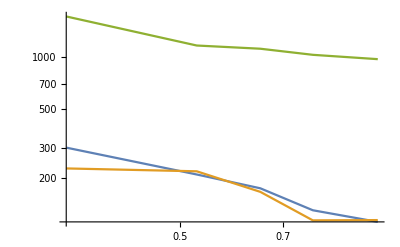

```mathematica
ENfromXmax[mass_,data_,LogMin_]:=Module[{distr},
datt=Select[data,#[[1]]==mass&];
EmaxVal=datt[[All,3]]//Max;
θlist=Table[x,{x,θminExp,θmaxExp,(θmaxExp-θminExp)/5}];
distr[θN_,EN_]=Abs[Evaluate[Interpolation[{#[[2]],#[[3]],#[[4]]+10^-90}&/@datt,InterpolationOrder->1][θN,EN]]];
DoubleDistrIntList[i_]:=Interpolation[ParallelTable[{EN,Quiet[NIntegrate[distr[θN,EN],{θN,θlist[[i]],θlist[[i+1]]},Method->"AdaptiveMonteCarlo"]]},{EN,Table[10^x,{x,Log10[1.1*mass],Log10[EmaxVal],(Log10[EmaxVal]-Log10[1.1*mass])/50.}]}],InterpolationOrder->1][EN];
θNdistrlist[EN_]=Table[{(θlist[[i]]+θlist[[i+1]])/2,DoubleDistrIntList[i]},{i,1,Length[θlist]-1,1}];
θEmaxList=Table[{θNdistrlist[EN][[i]][[1]],SortBy[Table[{EN,θNdistrlist[EN][[i]][[2]]},{EN,mass,EmaxVal,1}],-#[[2]]&][[1]][[1]]},{i,1,Length[θNdistrlist[EN]],1}];
θEmaxListInt[θN_]=Interpolation[θEmaxList,InterpolationOrder->1][θN];
NormVals=Table[NIntegrate[θNdistrlist[EN][[i]][[2]]+10^-90.,{EN,mass,EmaxVal},Method->"InterpolationPointsSubdivision"],{i,1,Length[θNdistrlist[EN]],1}];
cdf[es_,i_]:=1-1/NormVals[[i]] NIntegrate[θNdistrlist[EN][[i]][[2]],{EN,mass,es},Method->"InterpolationPointsSubdivision"];
cdftab[EN_]=Table[{θNdistrlist[EN][[i]][[1]],Interpolation[ParallelTable[{10^es,Quiet[cdf[10^es,i]]},{es,Log10[mass],Log10[EmaxVal],(Log10[EmaxVal]-Log10[mass])/50}],InterpolationOrder->1][EN]},{i,1,Length[θNdistrlist[EN]],1}];
logmin[θN_]=LogMin;
Estart[θN_]=Min[2*θEmaxListInt[θN],0.9*EmaxVal];
Emaxv[i_]:=If[NormVals[[i]]<10^-15,mass,10^(EN/.FindRoot[Log10[cdftab[10^EN][[i]][[2]]]==logmin[θEmaxList[[i]][[1]]],{EN,Log10[Estart[θEmaxList[[i]][[1]]]],Log10[θEmaxList[[i]][[2]]],Log10[EmaxVal]}])];
tabtemp=Table[{θEmaxList[[i]][[1]],Emaxv[i]},{i,1,Length[θEmaxList],1}];
tab=Join[{{θminExp,tabtemp[[1]][[2]]}},Drop[Drop[tabtemp,1],-1],{{θmaxExp,tabtemp[[-1]][[2]]}}];
10^(Interpolation[{Log10[#[[1]]],Log10[#[[2]]]}&/@tab,InterpolationOrder->1][Log10[θN]])
]
ENmaxBlock[data_,logmin_]:=Block[{},
mlist=Drop[data[[All,1]],-1];
EmaxTemp[mN_,θN_]=Max[mN,ENfromXmax[mlist[[1]],data,logmin],ENfromXmax[mlist[[-1]],data,logmin]];
θlist=Table[x,{x,θminExp,θmaxExp,(θmaxExp-θminExp)/10}];
10^(Interpolation[{#[[1]],Log10[#[[2]]],Log10[#[[3]]]}&/@Flatten[Table[{mN,θN,EmaxTemp[mN,θN]},{mN,mlist[[1]],mlist[[-1]],(mlist[[-1]]-mlist[[1]])/10},{θN,θlist}],{1,2}],InterpolationOrder->1][mN,Log10[θN]])
]
Do[ENmax[mN_,θN_,prod]=ENmaxBlock[DataDistrNfinal[prod],-7],{prod,ProductionList}];//AbsoluteTiming
LogLogPlot[{ENmax[1.5,θN,"D"],ENmax[1.5,θN,"B"],ENmax[1.5,θN,"W"]},{θN,θminExp,θmaxExp}]
```

## Number of events

## ϵ_geom× decay probability × decay products acceptance

### Preliminary definitions

```mathematica
PdecayDensity[mN_,U2_,θN_,EN_,zN_]=Exp[-zN/(Cos[θN]*ldecayN[mN,U2,EN])]/(Cos[θN]*ldecayN[mN,U2,EN]);
Do[IntegrandN[mN_,U2_,θN_,EN_,zN_,prod]=DoubleDistrN[mN,θN,EN,prod]*PdecayDensity[mN,U2,θN,EN,zN]*AzimuthalAcceptanceHNL[θN,zN]*DecayAcceptanceHNL[mN,θN,EN,zN],{prod,ProductionList}]
IntegralN[mN_,U2_,ProdChannel_]:=NIntegrate[Abs[IntegrandN[mN,U2,θN,EN,zN,ProdChannel]],{θN,θminExp,θmaxExp},{EN,mN,ENmax[mN,θN,ProdChannel]},{zN,zminθ[θN],zmaxθ[θN]},Method->"AdaptiveMonteCarlo"]
mNBval=1.4;
U2vall=8.2*10^-8;
IntegralN[mNBval,U2vall,"B"]
mNDval=1.4;
IntegralN[mNDval,U2vall,"D"]
mNWval=1.4;
If[MemberQ[{"LHC","FCC-hh"},FacilityGivenExperiment]==True,IntegralN[mNWval,U2vall,"W"]]
```

0.0000484719

0.0000949249

7.71883×10^-6

### Overall acceptance

{52.8667,Null}

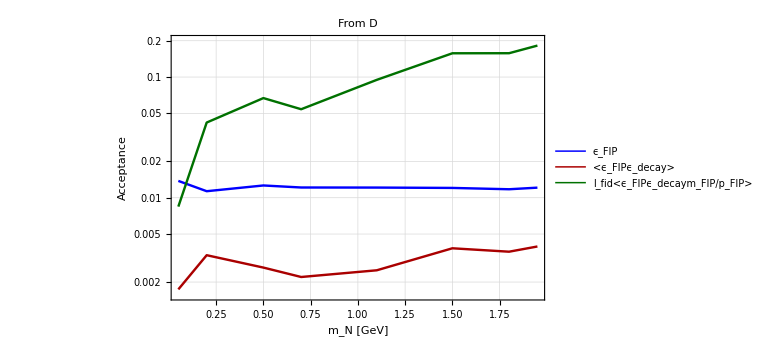
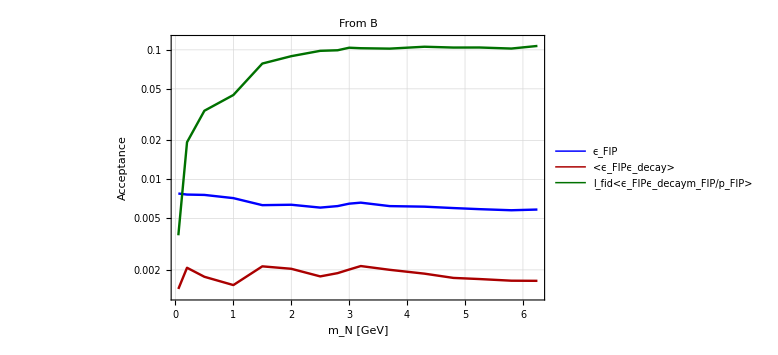
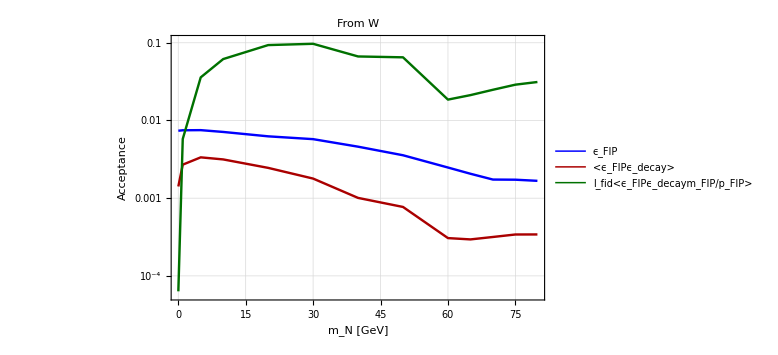

```mathematica
IntegrandWithϵAz[mN_,θN_,EN_,zN_,ProdChannel_]:=DoubleDistrN[mN,θN,EN,ProdChannel]/Cos[θN]*AzimuthalAcceptanceHNL[θN,zN]
IntegrandWithϵAzϵDec[mN_,θN_,EN_,zN_,ProdChannel_]:=DoubleDistrN[mN,θN,EN,ProdChannel]/Cos[θN]*AzimuthalAcceptanceHNL[θN,zN]*DecayAcceptanceHNL[mN,θN,EN,zN]
IntegrandWithϵAzϵDecγInv[mN_,θN_,EN_,zN_,ProdChannel_]:=DoubleDistrN[mN,θN,EN,ProdChannel]/Cos[θN]*AzimuthalAcceptanceHNL[θN,zN]*DecayAcceptanceHNL[mN,θN,EN,zN] mN/(√(EN^2-mN^2))
Do[IntegrandGeomAcceptance[mN_,θN_,EN_,zN_,ProdChannel]={IntegrandWithϵAz[mN,θN,EN,zN,ProdChannel],IntegrandWithϵAzϵDec[mN,θN,EN,zN,ProdChannel],IntegrandWithϵAzϵDecγInv[mN,θN,EN,zN,ProdChannel]},{ProdChannel,ProductionList}];
GeomAcceptanceN[mN_,i_,ProdChannel_]:=1/(zmaxExp-zminExp)NIntegrate[IntegrandGeomAcceptance[mN,θN,EN,zN,ProdChannel][[i]],{θN,θminExp,θmaxExp},{EN,mN,ENmax[mN,θN,ProdChannel]},{zN,zminθ[θN],zmaxθ[θN]},Method->"AdaptiveMonteCarlo"]
ϵGeomTabProdChannel[ProdChannel_]:=ParallelTable[{mN,GeomAcceptanceN[mN,1,ProdChannel],GeomAcceptanceN[mN,2,ProdChannel],(zmaxExp-zminExp)GeomAcceptanceN[mN,3,ProdChannel]},{mN,MassListDistrN[ProdChannel]}]
Do[ϵGeomTabs[prod]=ϵGeomTabProdChannel[prod],{prod,ProductionList}];//AbsoluteTiming
PlotAcc[ProdChannel_]:=ListLogPlot[{ϵGeomTabs[ProdChannel][[All,{1,2}]],ϵGeomTabs[ProdChannel][[All,{1,3}]],ϵGeomTabs[ProdChannel][[All,{1,4}]]},FrameStyle->Directive[Black, 22],PlotStyle->{{Thickness[0.003],Blue},{Thickness[0.003],Darker@Red},{Thickness[0.003],Darker@Darker@Green}},GridLines->Automatic,PlotRange->{MinMax[ϵGeomTabs[ProdChannel][[All,1]]],{0.9Min[Min[ϵGeomTabs[ProdChannel][[All,4]]],Min[ϵGeomTabs[ProdChannel][[All,3]]]],1.1Max[Max[ϵGeomTabs[ProdChannel][[All,2]]],Max[ϵGeomTabs[ProdChannel][[All,4]]]]}},Joined->True,Frame->True,ImageSize->Large,FrameLabel->{"m_N [GeV]","Acceptance"},PlotLabel-> Style[Row[{"From ",ProdChannel}], 20, Black],PlotLegends->Placed[{Style[#, 18]&/@{"ϵ_FIP","<ϵ_FIPϵ_decay>","l_fid<ϵ_FIPϵ_decaym_FIP/p_FIP>"}},{0.75,0.2}]]
Style[Row[Evaluate[Table[PlotAcc[prod],{prod,ProductionList}]]],ImageSizeMultipliers->{1,1,1,1}]
If[(DirectoryQ[FileNameJoin[{NotebookDirectory[],"Auxiliary data/HNLs",SelectedExperiment}]]//ToString)=="False",CreateDirectory[FileNameJoin[{NotebookDirectory[],"Auxiliary data/HNLs",SelectedExperiment}]]];
Do[FilenameAcceptance[prod]=ToString@StringForm["Acceptance_HNL_mixing-pattern_``-``-``_at_``_From_``.dat",Sequence@@{MixingPattern[[1]],MixingPattern[[2]],MixingPattern[[3]],SelectedExperiment,prod}];
Export[FileNameJoin[{NotebookDirectory[],"Auxiliary data/HNLs",SelectedExperiment,FilenameAcceptance[prod]}],ϵGeomTabs[prod],"Table"]
,{prod,ProductionList}]
```

## Number of events - brute-force integral

### Rough estimates of the upper and lower bounds

#### Definitions

InterpolatingFunction::dmval: Input value {0.0500047} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

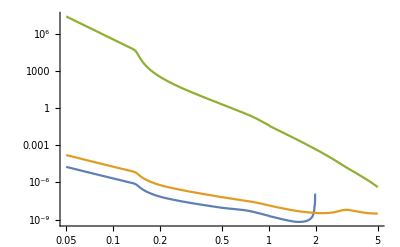

```mathematica
Do[U2minEstimate[mN_,prod]=((NpotGivenExperiment*χXtimesχXtoNtot[mN,prod]*Interpolation[ϵGeomTabs[prod][[All,{1,4}]],InterpolationOrder->1][mN])/(2.3ldecayN[mN,1,EN]*mN/(√(EN^2-mN^2))))^(-1/2.);
U2maxEstimate[mN_,prod]=Re[Evaluate[-ProductLog[-1,-2.3*b/a]/b/.{a-> NpotGivenExperiment*χXtimesχXtoNtot[mN,prod]*Interpolation[ϵGeomTabs[prod][[All,{1,3}]],InterpolationOrder->1][mN],b->zminExp/ldecayN[mN,1,ENmax[0.1,θminExp,prod]]}]],{prod,ProductionList}]
LogLogPlot[{U2minEstimate[mN,"D"],U2minEstimate[mN,"B"],U2maxEstimate[mN,"B"]},{mN,0.05,5}]
```

### Expression for the number of events

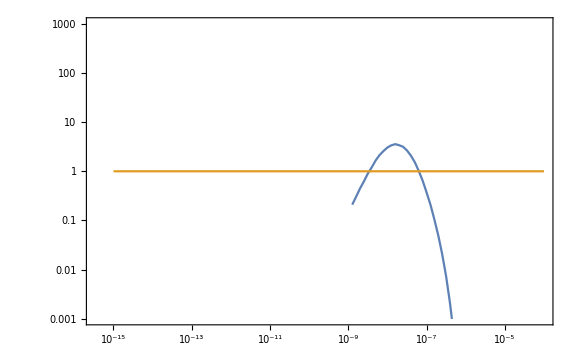

```mathematica
Nevents[mN_,U2_,ProdChannel_]:=If[mNmin[ProdChannel]≤mN≤mNmax[ProdChannel]&&BrVisMean[mN]!=0,If[0.3*U2minEstimate[mN,ProdChannel]<U2<1.8U2maxEstimate[mN,ProdChannel],NpotGivenExperiment*χXtimesχXtoNtot[mN,ProdChannel]*U2*IntegralN[mN,U2,ProdChannel],0],0]
tabNev[mN_,ProdChannel_]:=ParallelTable[{10^U2,Nevents[mN,10^U2,ProdChannel]},{U2,-12,-4,0.1}]
ListLogLogPlot[{tabNev[4,"B"],Table[{10^x,1},{x,-15,-4,0.1}]},Joined->True,Frame->True,ImageSize->Large,PlotRange->{All,{10^-3,1000}}]
```

## Number of events - alternative

### Preliminary definitions

#### In grid

```mathematica
(*Grid Subscript[m, S], Subscript[θ, S], Subscript[E, S], Subscript[z, S] for the initial acceptance data, logarithmized*)
InGridmϵ=DeleteDuplicates[ϵFullDecayDataFinal[[All,1]]];
InGridθϵ=DeleteDuplicates[ϵFullDecayDataFinal[[All,2]]];
InGridEϵ=DeleteDuplicates[ϵFullDecayDataFinal[[All,3]]];
InGridzϵ=DeleteDuplicates[ϵFullDecayDataFinal[[All,4]]];
(*Array of values of the initial acceptance data, reshaped*)
ϵvals=ArrayReshape[ϵFullDecayDataFinal[[All,5]],{Length[InGridmϵ],Length[InGridθϵ],Length[InGridEϵ],Length[InGridzϵ]}];
(*_________________________________________________________________*)
(*Grid Subscript[m, S], Subscript[θ, S], Subscript[E, S] for the initial FIP distribution data, logarithmized*)
DataLogarithmiedComp=Hold@Compile[{{data,_Real,2}},Table[If[data[[i]][[4]]==0,-90.,Log10[data[[i]][[4]]]],{i,1,Length[data],1}],CompilationTarget->"C",RuntimeOptions->"Speed"]//ReleaseHold
BlockGridsValsDistr[ProdChannel_]:=Module[{GridIn,vals},
GridIn=Log10[DeleteDuplicates[DataDistrNfinal[ProdChannel][[All,#]]]&/@{1,2,3}];
vals=ArrayReshape[DataLogarithmiedComp[DataDistrNfinal[ProdChannel]],{Length[GridIn[[1]]],Length[GridIn[[2]]],Length[GridIn[[3]]]}];
{GridIn,vals}
]
Do[{GridInFinal[prod],DistrVals[prod]}=BlockGridsValsDistr[prod],{prod,ProductionList}];//AbsoluteTiming
```

CompiledFunction[…]

{0.461994,Null}

#### Out grid

```mathematica
(*Grid Subscript[θ, S], Subscript[z, S] for the final acceptance data, logarithmized*)
OutGridθfinal=(*InGridθϵ*)Log10[Table[x,{x,10^Min[InGridθϵ],10^Max[InGridθϵ],(10^Max[InGridθϵ]-10^Min[InGridθϵ])/30}]];
OutGridzfinal=Log10[Table[x,{x,10^InGridzϵ[[1]],10^InGridzϵ[[-1]],Min[(10^InGridzϵ[[-1]]-10^InGridzϵ[[1]])/5,Max[0.5,(10^InGridzϵ[[-1]]-10^InGridzϵ[[1]])/30]]}]](*InGridzϵ*);
ΔxVals[list_]:=Join[{(list[[2]]-list[[1]])/2},Table[list[[i]]-list[[i-1]],{i,2,Length[list],1}]];
Δθvals=ΔxVals[10^OutGridθfinal];
Δzvals=ΔxVals[10^OutGridzfinal];
(*Final energy grid. Mass- and production channel-dependent*)
StepEtemp[Efip_]=Piecewise[{{0.3,Efip≤2.5},{0.5,2.5<Efip<35},{2,35≤Efip≤50},{4,50<Efip<160},{5,160≤Efip<300},{40,300≤Efip<700},{50,700≤Efip<2000},{200,2000≤Efip<4000},{400,4000≤Efip<7000},{500,7000≤Efip≤50000}}];
OutGridEnergy[m_,ProdChannel_]:=Block[{},
With[{start=1.01m,end=ENmax[m,θminExp,ProdChannel]},
Log10[NestWhileList[#+StepEtemp[#]&,start,#≤end&,1,∞,-1]]]//N
]
ΔxValsTotComp=Hold@Compile[{{Δθvals,_Real,1},{ΔEvals,_Real,1},{Δzvals,_Real,1}},Table[{Δθvals[[i]]*ΔEvals[[j]]*Δzvals[[k]]},{i,1,Length[Δθvals]},{j,1,Length[ΔEvals]},{k,1,Length[Δzvals]}],CompilationTarget->"C",RuntimeOptions->"Speed"]//ReleaseHold;
```

### Number of events

```mathematica
(*Block that computes the grid Subscript[θ, S],Subscript[E, S],Subscript[z, S], Subscript[ϵ, Full]×Subscript[f, Subscript[θ, S],Subscript[E, S]]*)
TableIntegrandDiscret[m_,ProdChannel_]:=Block[{},
OutGridEfinal=OutGridEnergy[N[m],ProdChannel];
ΔEvals=ΔxVals[10^OutGridEfinal];
ΔxValsTot=Flatten[ΔxValsTotComp[Δθvals,ΔEvals,Δzvals],{1,2,3}];
OutGridFinal=Tuples[{{Log10[N[m]]},OutGridθfinal,OutGridEfinal,OutGridzfinal}];
OutGridFinal1=10^OutGridFinal[[All,{2,3,4}]];
gϵ={InGridmϵ,InGridθϵ,InGridEϵ,InGridzϵ};
xgϵ={{Log10[N[m]]},OutGridθfinal,OutGridEfinal,OutGridzfinal};
xigϵ=MapThread[Interpolation[Transpose@{#,Range@Length@#},InterpolationOrder->1][#2]&,{gϵ,xgϵ}];
ϵResult=10^Flatten@cf4[Sequence@@xigϵ,ϵvals];
gDistr={GridInFinal[ProdChannel][[1]],GridInFinal[ProdChannel][[2]],GridInFinal[ProdChannel][[3]]};
xgDistr={{Log10[N[m]]},OutGridθfinal,OutGridEfinal};
xigDistr=MapThread[Interpolation[Transpose@{#,Range@Length@#},InterpolationOrder->1][#2]&,{gDistr,xgDistr}];
DistrResult=10^Flatten@cf3[Sequence@@xigDistr,DistrVals[ProdChannel]];
TabTemp0=Join[OutGridFinal1,List/@Flatten[DistrResult Partition[ϵResult,Length[OutGridzfinal]]],ΔxValsTot,2]
]
(*Values Subscript[f, FIP]×Subscript[ϵ, FIP]×Exp[-Subscript[z, FIP]/(cos(Subscript[θ, FIP])Subscript[cτ, FIP] Subscript[p, FIP]/Subscript[m, FIP])]/(cos(Subscript[θ, FIP])Subscript[cτ, FIP] Subscript[p, FIP]/Subscript[m, FIP])×Subscript[ϵ, decay] Subscript[Δz, FIP] Subscript[ΔE, FIP] Subscript[Δθ, FIP] for the grid of values Subscript[θ, FIP], Subscript[E, FIP], Subscript[z, FIP] fixed values of Subscript[cτ, FIP] and Subscript[m, FIP]*)
tableprefac=Hold@Compile[{{tabb,_Real,1},{m,_Real},{cτ,_Real}},Module[{angles,energies,zv,values,Δs,prefactor},
angles=Compile`GetElement[tabb,1];
energies=Compile`GetElement[tabb,2];
zv=Compile`GetElement[tabb,3];
values=Compile`GetElement[tabb,4];
Δs=Compile`GetElement[tabb,5];
prefactor=Exp[-zv/(Cos[angles]*cτ*(√(energies^2-m^2))/m)]/(Cos[angles]*cτ*(√(energies^2-m^2))/m);
prefactor*Δs*values],CompilationTarget->"C",RuntimeOptions->"Speed",Parallelization->"True",RuntimeAttributes->{Listable}]//ReleaseHold;
(*Summation of the values above*)
sumcompile=Hold@Compile[{{tabcτm,_Real,1}},Total[tabcτm],CompilationTarget->"C",RuntimeOptions->"Speed",Parallelization->"True"]//ReleaseHold;
{mminϵ,mmaxϵ}=10^MinMax[InGridmϵ]
(*Number of events*)
NeventsDiscret[m_,ProdChannel_,U2list_]:=Module[{NevDiscret,NpotTimesχval},
If[Max[mNmin[ProdChannel],mminϵ]<m<Min[mNmax[ProdChannel],mmaxϵ],
integrandtab=TableIntegrandDiscret[m,ProdChannel];
NpotTimesχval[U2_]=NpotGivenExperiment*χXtimesχXtoNtot[m,ProdChannel]*U2;
{lowerbound,upperbound}={U2minEstimate[m,ProdChannel],U2maxEstimate[m,ProdChannel]};
brvis=BrVisMean[m];
NevDiscret[U2_]:=If[brvis!=0,If[0.3lowerbound<U2<1.5upperbound,NpotTimesχval[U2]*brvis*sumcompile[tableprefac[integrandtab,m,cτN[m,U2]]],0],0];
Table[{m,U2list[[i]],NevDiscret[U2list[[i]]]},{i,1,Length[U2list],1}],Table[{m,U2list[[i]],0},{i,1,Length[U2list],1}]]
]
```

{0.02,80.}

#### Test

```mathematica
mtest=1.57;
ProdTest="D";
U2list=(*{10^-12,3*10^-12,5*10^-12,10^-11,5*10^-11,10^-10,5*10^-10,10^-9,5*10^-9,10^-8,2*10^-8,4*10^-8,10^-7,5*10^-7,6*10^-7,7*10^-7,8*10^-7,9*10^-7,10^-6,2*10^-6}//N*)Table[10^x,{x,-12.,-3.,0.1}];
dat1=NeventsDiscret[mtest,ProdTest,U2list];//AbsoluteTiming
dat2=ParallelTable[{U2list[[i]],cτN[mtest,U2list[[i]]],Nevents[mtest,U2list[[i]],ProdTest]},{i,1,Length[U2list],1}];//AbsoluteTiming
Join[dat1,dat2[[All,{3,2}]],2]//TableForm
```

{0.635214,Null}

{49.3593,Null}

1.57 | 1.×10^-12 | 0 | 0 | 5.63692×10^7
1.57 | 1.25893×10^-12 | 0 | 0 | 4.47756×10^7
1.57 | 1.58489×10^-12 | 0 | 0 | 3.55665×10^7
1.57 | 1.99526×10^-12 | 0 | 0 | 2.82515×10^7
1.57 | 2.51189×10^-12 | 0 | 0 | 2.2441×10^7
1.57 | 3.16228×10^-12 | 0 | 0 | 1.78255×10^7
1.57 | 3.98107×10^-12 | 0 | 0 | 1.41593×10^7
1.57 | 5.01187×10^-12 | 0 | 0 | 1.12471×10^7
1.57 | 6.30957×10^-12 | 0 | 0 | 8.93391×10^6
1.57 | 7.94328×10^-12 | 0 | 0 | 7.09646×10^6
1.57 | 1.×10^-11 | 0 | 0 | 5.63692×10^6
1.57 | 1.25893×10^-11 | 0 | 0 | 4.47756×10^6
1.57 | 1.58489×10^-11 | 0 | 0 | 3.55665×10^6
1.57 | 1.99526×10^-11 | 0 | 0 | 2.82515×10^6
1.57 | 2.51189×10^-11 | 0 | 0 | 2.2441×10^6
1.57 | 3.16228×10^-11 | 0 | 0 | 1.78255×10^6
1.57 | 3.98107×10^-11 | 0 | 0 | 1.41593×10^6
1.57 | 5.01187×10^-11 | 0 | 0 | 1.12471×10^6
1.57 | 6.30957×10^-11 | 0 | 0 | 893391.
1.57 | 7.94328×10^-11 | 0 | 0 | 709646.
1.57 | 1.×10^-10 | 0 | 0 | 563692.
1.57 | 1.25893×10^-10 | 0 | 0 | 447756.
1.57 | 1.58489×10^-10 | 0 | 0 | 355665.
1.57 | 1.99526×10^-10 | 0.188582 | 0.200509 | 282515.
1.57 | 2.51189×10^-10 | 0.298866 | 0.246378 | 224410.
1.57 | 3.16228×10^-10 | 0.473637 | 0.495974 | 178255.
1.57 | 3.98107×10^-10 | 0.750598 | 0.685572 | 141593.
1.57 | 5.01187×10^-10 | 1.18949 | 1.20631 | 112471.
1.57 | 6.30957×10^-10 | 1.88495 | 1.99691 | 89339.1
1.57 | 7.94328×10^-10 | 2.98691 | 3.08717 | 70964.6
1.57 | 1.×10^-9 | 4.73289 | 4.488 | 56369.2
1.57 | 1.25893×10^-9 | 7.49903 | 7.45476 | 44775.6
1.57 | 1.58489×10^-9 | 11.881 | 12.5927 | 35566.5
1.57 | 1.99526×10^-9 | 18.8218 | 15.2038 | 28251.5
1.57 | 2.51189×10^-9 | 29.8139 | 30.4553 | 22441.
1.57 | 3.16228×10^-9 | 47.2187 | 49.189 | 17825.5
1.57 | 3.98107×10^-9 | 74.7707 | 73.8097 | 14159.3
1.57 | 5.01187×10^-9 | 118.372 | 124.397 | 11247.1
1.57 | 6.30957×10^-9 | 187.345 | 188.69 | 8933.91
1.57 | 7.94328×10^-9 | 296.4 | 302.218 | 7096.46
1.57 | 1.×10^-8 | 468.725 | 482.688 | 5636.92
1.57 | 1.25893×10^-8 | 740.812 | 787.916 | 4477.56
1.57 | 1.58489×10^-8 | 1170. | 1126.05 | 3556.65
1.57 | 1.99526×10^-8 | 1846.17 | 1900.67 | 2825.15
1.57 | 2.51189×10^-8 | 2909.79 | 2589.34 | 2244.1
1.57 | 3.16228×10^-8 | 4579.65 | 3717.11 | 1782.55
1.57 | 3.98107×10^-8 | 7194.86 | 7412.36 | 1415.93
1.57 | 5.01187×10^-8 | 11278. | 12161.7 | 1124.71
1.57 | 6.30957×10^-8 | 17628.5 | 18785. | 893.391
1.57 | 7.94328×10^-8 | 27457.2 | 28926.8 | 709.646
1.57 | 1.×10^-7 | 42576.4 | 36866.7 | 563.692
1.57 | 1.25893×10^-7 | 65655.2 | 68551. | 447.756
1.57 | 1.58489×10^-7 | 100545. | 94404.3 | 355.665
1.57 | 1.99526×10^-7 | 152650. | 146607. | 282.515
1.57 | 2.51189×10^-7 | 229286. | 244742. | 224.41
1.57 | 3.16228×10^-7 | 339852. | 343604. | 178.255
1.57 | 3.98107×10^-7 | 495555. | 488811. | 141.593
1.57 | 5.01187×10^-7 | 708238. | 745743. | 112.471
1.57 | 6.30957×10^-7 | 987761. | 1.01241×10^6 | 89.3391
1.57 | 7.94328×10^-7 | 1.33753×10^6 | 1.22799×10^6 | 70.9646
1.57 | 1.×10^-6 | 1.74836×10^6 | 1.78451×10^6 | 56.3692
1.57 | 1.25893×10^-6 | 2.19209×10^6 | 2.20862×10^6 | 44.7756
1.57 | 1.58489×10^-6 | 2.61831×10^6 | 2.6926×10^6 | 35.5665
1.57 | 1.99526×10^-6 | 2.95861×10^6 | 2.86467×10^6 | 28.2515
1.57 | 2.51189×10^-6 | 3.14134×10^6 | 3.17793×10^6 | 22.441
1.57 | 3.16228×10^-6 | 3.11482×10^6 | 3.12291×10^6 | 17.8255
1.57 | 3.98107×10^-6 | 2.8697×10^6 | 2.82696×10^6 | 14.1593
1.57 | 5.01187×10^-6 | 2.4477×10^6 | 2.44251×10^6 | 11.2471
1.57 | 6.30957×10^-6 | 1.92952×10^6 | 1.93069×10^6 | 8.93391
1.57 | 7.94328×10^-6 | 1.40674×10^6 | 1.40393×10^6 | 7.09646
1.57 | 0.00001 | 952210. | 938204. | 5.63692
1.57 | 0.0000125893 | 603309. | 585621. | 4.47756
1.57 | 0.0000158489 | 362574. | 358936. | 3.55665
1.57 | 0.0000199526 | 210475. | 211388. | 2.82515
1.57 | 0.0000251189 | 120498. | 122878. | 2.2441
1.57 | 0.0000316228 | 69341.8 | 70945.9 | 1.78255
1.57 | 0.0000398107 | 40571.3 | 41630.8 | 1.41593
1.57 | 0.0000501187 | 24064.5 | 24238.4 | 1.12471
1.57 | 0.0000630957 | 14154.9 | 14249.2 | 0.893391
1.57 | 0.0000794328 | 7940.05 | 8040. | 0.709646
1.57 | 0.0001 | 4044.54 | 3983.87 | 0.563692
1.57 | 0.000125893 | 1774.62 | 1716.76 | 0.447756
1.57 | 0.000158489 | 634.707 | 606.154 | 0.355665
1.57 | 0.000199526 | 174.406 | 162.926 | 0.282515
1.57 | 0.000251189 | 34.4221 | 31.3679 | 0.22441
1.57 | 0.000316228 | 4.50005 | 4.19076 | 0.178255
1.57 | 0.000398107 | 0.352694 | 0.31883 | 0.141593
1.57 | 0.000501187 | 0.0146829 | 0.0134736 | 0.112471
1.57 | 0.000630957 | 0.000281476 | 0.000252927 | 0.0893391
1.57 | 0.000794328 | 2.11002×10^-6 | 1.89393×10^-6 | 0.0709646
1.57 | 0.001 | 5.44485×10^-9 | 4.63255×10^-9 | 0.0563692

### Differential number of events

CompiledFunction[…]

{1.313,1703.01}

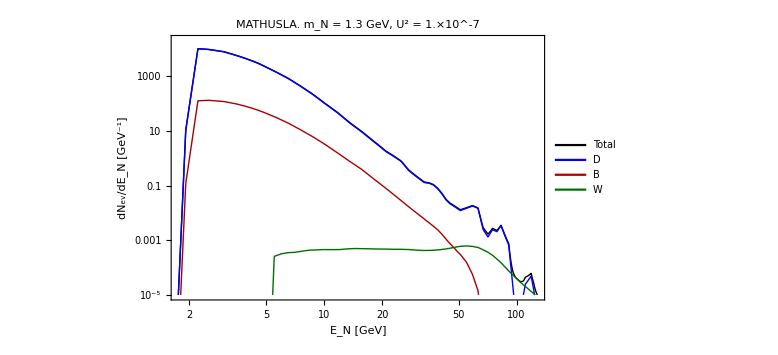

```mathematica
(*The same as tableprefac but also including the grid*)
tableGridPrefac=Hold@Compile[{{tabb,_Real,2},{mS,_Real},{cτ,_Real}},{#[[1]],#[[2]],#[[3]],Exp[-#[[3]]/(Cos[#[[1]]]*cτ*(√((#[[2]])^2-mS^2))/mS)]/(Cos[#[[1]]]*cτ*(√((#[[2]])^2-mS^2))/mS)#[[4]]*#[[5]]}&/@tabb,CompilationTarget->"C",RuntimeOptions->"Speed",Parallelization->"True",RuntimeAttributes->{Listable}]//ReleaseHold;
(*Summation returning the differential number of events X, df/dX *)
NdiffCompiled=Hold@Compile[{{tabNdiff,_Real,2},{GridQuantity,_Real,1},{LengthPerVariable,_Integer},{NPoTtimesPprod,_Real}},Table[{tabNdiff[[LengthPerVariable*(i-1)+1]][[1]],NPoTtimesPprod*Sum[tabNdiff[[LengthPerVariable*(i-1)+j]][[4]],{j,1,LengthPerVariable,1}]},{i,1,Length[GridQuantity],1}],CompilationTarget->"C",RuntimeOptions->"Speed",Parallelization->"True"]//ReleaseHold
(*Variable = "E_X","x_x","θ_X". The number belongs to the column in the tabulated data*)
iVal:=Association[{"E_X" ->2,"θ_X"->1,"x_x"->3}]
(*Differential number of events*)
NeventsDifferentialDiscret[m_,ProdChannel_,U2_,Variable_]:=Module[{NpotTimesχval},
ival=iVal[Variable];
NpotTimesχval=NpotGivenExperiment*χXtimesχXtoNtot[m,ProdChannel]*U2;
tablegrid0=TableIntegrandDiscret[m,ProdChannel];
Δxvals:=Association[{"E_X"->ΔEvals,"θ_X"-> Δθvals,"x_X"-> Δzvals}];
Δxval=Δxvals[Variable];
cτVal=cτN[m,U2];
brvis=BrVisMean[m];
ilist=DeleteDuplicates[{ival,1,2,3}];
tablegrid1=SortBy[{#[[ilist[[1]]]],#[[ilist[[2]]]],#[[ilist[[3]]]],#[[4]]}&/@tableGridPrefac[tablegrid0,m,cτVal],{#[[1]],#[[2]],#[[3]]}&];
GridQuantity=tablegrid1[[All,1]]//DeleteDuplicates;
LengthPerVariable=Length[tablegrid1]/Length[GridQuantity];
tab1=NdiffCompiled[tablegrid1,GridQuantity,LengthPerVariable,NpotTimesχval*brvis];
Join[tab1[[All,{1}]],Partition[tab1[[All,2]]*Δxval^-1,1],2]
]
mvaltest=1.3;
U2test=10^-7.;
quantity="E_X";
LegendX:=Association[{"E_X"->"E_N [GeV]","θ_X"->"θ_N [rad]","x_X"-> "z_N [m]"}]
LegendY:=Association[{"E_X"->"dN_ev/dE_N [GeV^-1]","θ_X"->"dN_ev/dθ_N [rad^-1]","x_X"-> "dN_ev/dz_N [m^-1]"}]
proclisttemp={};
Do[If[Max[mNmin[prod],mminϵ]<mvaltest<Min[mNmax[prod],mmaxϵ],
proclisttemp=Join[proclisttemp,{prod}];
NdiffData[prod]=NeventsDifferentialDiscret[mvaltest,prod,U2test,quantity];
XvalminmaxNdiff=Select[NdiffData[prod],#[[2]]>10^-40&][[All,1]]//MinMax;
NdiffInt[X_,prod]=If[XvalminmaxNdiff[[1]]<X<XvalminmaxNdiff[[2]],Evaluate[10^Interpolation[{Log10[#[[1]]],Log10[#[[2]]+10^-90]}&/@NdiffData[prod],InterpolationOrder->1][Log10[X]]],0]],{prod,ProductionList}];
NdiffInt[X_,"Total"]=Sum[NdiffInt[X,prod],{prod,proclisttemp}];
LegendList=Join[{"Total"},proclisttemp];
QuantityMinMax=Flatten[Table[MinMax[NdiffData[prod][[All,1]]],{prod,proclisttemp}],1]//MinMax
ValueMinMax=Max[Max[NdiffData[#][[All,2]]]&/@ProductionList];
LogLogPlot[Evaluate[Table[NdiffInt[X,prod],{prod,LegendList}]],{X,QuantityMinMax[[1]],QuantityMinMax[[2]]},Frame->True,ImageSize->Large,PlotRange->{All,{10^-5,2ValueMinMax}},PlotStyle->{{Thick,Black},{Thick,Blue},{Thick,Darker@Red},{Thick,Darker@Darker@Green},{Thick,Darker@Cyan},{Thick,Magenta},{Thick,Blue,Dashing[0.02]},{Thick,Darker@Red,Dashing[0.02]},{Thick,Darker@Darker@Green,Dashing[0.02]}},PlotLegends->Placed[Style[#,20]&/@LegendList,{0.85,0.7}],FrameLabel->{LegendX[quantity] ,LegendY[quantity]},FrameStyle->Directive[Black, 23],PlotLabel->Style[Row[{SelectedExperiment,". m_N = ",mvaltest," GeV, U^2 = ",U2test}],20,Black]]
```

# Exporting tabulated number of events

## Definitions

```mathematica
If[(DirectoryQ[FileNameJoin[{NotebookDirectory[],"Tabulated Nevents"}]]//ToString)=="False",CreateDirectory[FileNameJoin[{NotebookDirectory[],"Tabulated Nevents"}]]]
If[(DirectoryQ[FileNameJoin[{NotebookDirectory[],"Tabulated Nevents/HNLs"}]]//ToString)=="False",CreateDirectory[FileNameJoin[{NotebookDirectory[],"Tabulated Nevents/HNLs"}]]]
If[(DirectoryQ[FileNameJoin[{NotebookDirectory[],"Tabulated Nevents/HNLs",SelectedExperiment}]]//ToString)=="False",CreateDirectory[FileNameJoin[{NotebookDirectory[],"Tabulated Nevents/HNLs",SelectedExperiment}]]]
Print["List of filenames with exported tabulated number of events"]
Do[FilenameNevents[prod]=ToString@StringForm["Nevents_HNL_MixingPattern_``-``-``_type_``_at_``_Npot=``_From_``.dat",Sequence@@{ToString[MixingPattern[[1]]],ToString[MixingPattern[[2]]],ToString[MixingPattern[[3]]],HNLtype,SelectedExperiment,NpotGivenExperiment//CForm//ToString,prod}],{prod,ProductionList}]
Table[FilenameNevents[prod],{prod,ProductionList}]//TableForm
mNlistExport["D"]=Table[mx,{mx,0.051,1.951,0.02}];
mNlistExport["B"]=Table[mx,{mx,0.051,6.301,0.02}];
mNlistExport["W"]=If[FacilityGivenExperiment=="LHC"||FacilityGivenExperiment=="FCC-hh",Join[Table[10^mx,{mx,Log10[0.051],Log10[79.99],(Log10[79.99]-Log10[0.051])/90}]]];
U2range=Table[10^x,{x,-13,-3,0.03}];
```

List of filenames with exported tabulated number of events

Nevents_HNL_MixingPattern_1.-0.-0._type_Majorana_at_MATHUSLA_Npot=2.16e17_From_D.dat
Nevents_HNL_MixingPattern_1.-0.-0._type_Majorana_at_MATHUSLA_Npot=2.16e17_From_B.dat
Nevents_HNL_MixingPattern_1.-0.-0._type_Majorana_at_MATHUSLA_Npot=2.16e17_From_W.dat

## Exporting

## Common definition

```mathematica
BlockExport[ProdChannel_]:=Block[{},
If[Select[ProductionList,#==ProdChannel&]=={},,
mlist=mNlistExport[ProdChannel];
TabFrom=Monitor[Table[NeventsDiscret[mlist[[k]],ProdChannel,U2range],{k,1,Length[mlist],1}],Row[{ProgressIndicator[k,{1,Length[mlist]}],"i = ",k,"/",Length[mlist],", m = ",mlist[[k]]," GeV"}," "]];
Export[FileNameJoin[{NotebookDirectory[],"Tabulated Nevents/HNLs",SelectedExperiment,FilenameNevents[ProdChannel]}],Flatten[TabFrom,1],"Table"]]
]
```

## From D

```mathematica
BlockExport["D"];//AbsoluteTiming
```

InterpolatingFunction::dmval: Input value {0.051} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

{173.629,Null}

## From B

```mathematica
BlockExport["B"];//AbsoluteTiming
```

InterpolatingFunction::dmval: Input value {0.051} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

{327.42,Null}

## From W

```mathematica
BlockExport["W"];//AbsoluteTiming
```

{58.4734,Null}

# Computing sensitivities

## Specifying the experiment and the HNL model

```mathematica
If[(DirectoryQ[FileNameJoin[{NotebookDirectory[],"Sensitivity domains"}]]//ToString)=="False",CreateDirectory[FileNameJoin[{NotebookDirectory[],"Sensitivity domains"}]]]
If[(DirectoryQ[FileNameJoin[{NotebookDirectory[],"Sensitivity domains","HNLs"}]]//ToString)=="False",CreateDirectory[FileNameJoin[{NotebookDirectory[],"Sensitivity domains","HNLs"}]]]
NeventsDirectory=FileNameJoin[{NotebookDirectory[],"Tabulated Nevents/HNLs"}];
ExperimentDirectoriesListNevents=Select[FileNames["*",NeventsDirectory,1],DirectoryQ];
Print["List of available experiments with tabulated N_events for HNLs:"]
ExperimentsListNevents=Table[FileNameTake[ExperimentDirectoriesListNevents[[i]],-1],{i,1,Length[ExperimentDirectoriesListNevents],1}]//Sort;
ExperimentsListNevents//TableForm
If[Length[ExperimentsListNevents]==0,Print["No experiment is available, generate first the acceptance for the given experiment using module 1"]]
Print["Selected experiment:"]
dropdownDialog[list_,phrase_]:=DialogInput[{choice=""},Column[{TextCell[phrase],PopupMenu[Dynamic[choice],list],Button["OK",DialogReturn[choice]]}]]
If[Length[ExperimentsListNevents]≠0,GivenExperimentForSensitivityComputation=dropdownDialog[ExperimentsListNevents,"Select the experiment:"]]

CondANUBIS=MemberQ[{"ANUBIS-1","ANUBIS-2","ANUBIS-3"},GivenExperimentForSensitivityComputation];
If[CondANUBIS==True,Print["One of the modules of ANUBIS is chosen. The full sensitivity includes three modules. The importing will be over all modules, so for all ot the the sensitivity has to be computed"]]
If[CondANUBIS==False,GivenExperimentForSensitivityComputationList={GivenExperimentForSensitivityComputation},GivenExperimentForSensitivityComputationList={"ANUBIS-1","ANUBIS-2","ANUBIS-3"}];
filesNevents={};
Do[filesNevents=Join[filesNevents,FileNames["*.dat",FileNameJoin[{NotebookDirectory[],"Tabulated Nevents/HNLs",exp}]]],{exp,GivenExperimentForSensitivityComputationList}];
FilenamesNevents=Table[Last@FileNameSplit@filesNevents[[i]],{i,1,Length[filesNevents],1}];
FilenameParametersTemp[i_]:=StringCases[FilenamesNevents[[i]],"Nevents_HNL_MixingPattern_"~~mixinge__~~"-"~~mixingμ__~~"-"~~mixingτ__~~"_type_"~~type__~~"_at_"~~experiment__~~"_Npot="~~Npot__~~"_From_"~~mother__~~".dat":>{mixinge//ToExpression,mixingμ//ToExpression,mixingτ//ToExpression,type,experiment,Npot,mother}][[1]]
FilenameParameters=Table[FilenameParametersTemp[i],{i,1,Length[FilenamesNevents],1}];
NpotDefault=Internal`StringToMReal[FilenameParameters[[1]][[6]]];
TableHNLtype=DeleteDuplicates[FilenameParameters[[All,{1,2,3,4}]]];
Join[{{"U_e^2/U^2","U_μ^2/U^2","U_τ^2/U^2","HNL type"}},TableHNLtype]//TableForm
dataSelected=dropdownDialog[TableHNLtype,"Choose available HNL mixing pattern and type (xe,xμ,xτ,Type):"]
Print["Selected mixing pattern:"]
SelectedMixingPattern={dataSelected[[1]]//ToExpression,dataSelected[[2]]//ToExpression,dataSelected[[3]]//ToExpression}
Print["Selected type - Dirac or Majorana:"]
SelectedHNLtype=dataSelected[[4]]
Print["Data to import:"]
ParametersToImport=Select[FilenameParameters,#[[1]]==dataSelected[[1]]&&#[[2]]==dataSelected[[2]]&&#[[3]]==dataSelected[[3]]&&#[[4]]==dataSelected[[4]]&];
ParametersToImport//TableForm
```

C:\Users\miksi\Dropbox\Science 2\HNL and scalar phenomenology\_SensCalc\Sensitivity domains\HNLs

List of available experiments with tabulated N_events for HNLs:

MATHUSLA
SHADOWS-LoI
SHiP-ECN3

Selected experiment:

SHiP-ECN3

U_e^2/U^2 | U_μ^2/U^2 | U_τ^2/U^2 | HNL type
0. | 0. | 1. | Majorana
1. | 0. | 0. | Majorana

{1.,0.,0.,Majorana}

Selected mixing pattern:

{1.,0.,0.}

Selected type - Dirac or Majorana:

Majorana

Data to import:

1. | 0. | 0. | Majorana | SHiP-ECN3 | 2.e20 | B
1. | 0. | 0. | Majorana | SHiP-ECN3 | 2.e20 | D

## Sensitivity evaluation

## Data importing and interpolation

```mathematica
NevData[i_]:=Block[{},
filetoimport=ToString@StringForm["Nevents_HNL_MixingPattern_``-``-``_type_``_at_``_Npot=``_From_``.dat",Sequence@@ParametersToImport[[i]]];
dat=Import[FileNameJoin[{NotebookDirectory[],"Tabulated Nevents/HNLs",ParametersToImport[[i]][[5]],filetoimport}]]]
Do[dataimported[i]=NevData[i];
{mNminMax[i],U2minMax[i]}={MinMax[dataimported[i][[All,1]]],MinMax[dataimported[i][[All,2]]]},{i,1,Length[ParametersToImport],1}];
{mNminMaxOverall,U2minmaxOverall}={MinMax[Join[##,1]&@@Table[mNminMax[i],{i,Length[ParametersToImport]}]],MinMax[Join[##,1]&@@Table[U2minMax[i],{i,Length[ParametersToImport]}]]};
Do[NevInt[mN_,U2_,i]=If[mNminMax[i][[1]]≤mN≤mNminMax[i][[2]]&&U2minMax[i][[1]]≤U2≤U2minMax[i][[2]],Evaluate[10^(Interpolation[{Log10[#[[1]]],Log10[#[[2]]],Log10[#[[3]]+10^-90]}&/@dataimported[i],InterpolationOrder->1][Log10[mN],Log10[U2]])],0],{i,1,Length[ParametersToImport],1}];
NevIntTot[mN_,U2_]=Sum[NevInt[mN,U2,i],{i,1,Length[ParametersToImport],1}];
ExperimentFolder=If[CondANUBIS==True,"ANUBIS",GivenExperimentForSensitivityComputation];
If[(DirectoryQ[FileNameJoin[{NotebookDirectory[],"Sensitivity domains","HNLs",ExperimentFolder}]]//ToString)=="False",CreateDirectory[FileNameJoin[{NotebookDirectory[],"Sensitivity domains","HNLs",ExperimentFolder}]]]
```

C:\Users\miksi\Dropbox\Science 2\HNL and scalar phenomenology\_SensCalc\Sensitivity domains\HNLs\SHiP-ECN3

## N_events density plot

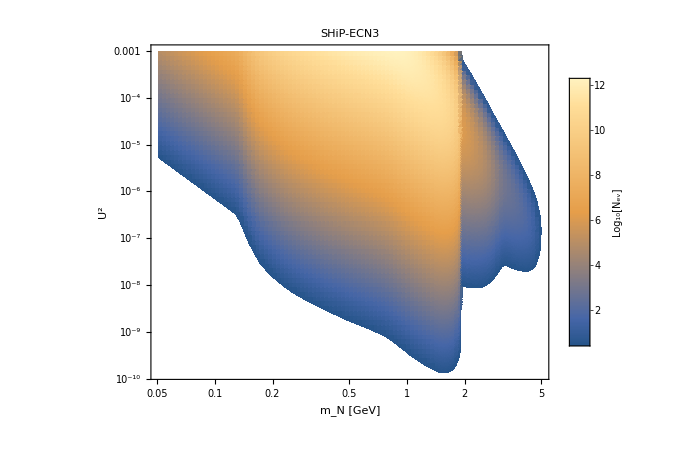

```mathematica
Nevmax=Max[Table[Max[dataimported[i][[All,3]]],{i,1,Length[ParametersToImport],1}]];
plot=DensityPlot[Evaluate[Log10[NevIntTot[mN,U2]]],{mN,mNminMaxOverall[[1]],mNminMaxOverall[[2]]},{U2,U2minmaxOverall[[1]],U2minmaxOverall[[2]]},ScalingFunctions->{"Log","Log"},AspectRatio->0.78,PlotRange->{All,All,{Log10[2.3],Log10[Nevmax]}},ImageSize->Large,FrameLabel->{"m_N [GeV]","U^2"}, Frame-> True, FrameStyle->Directive[Black, 25],PlotPoints->100,PlotLegends->Placed[BarLegend[{Automatic,{Log10[2.3],Log10[Nevmax]}},LegendMarkerSize->340,LegendLabel->Placed["Log_10[N_ev]",Bottom],LabelStyle->{FontSize->22},Method->{FrameStyle->Black,AxesStyle->None,TicksStyle->Black}],Right],PlotLabel->Style[Row[{ExperimentFolder}],20,Black](*,FrameTicks->{{Automatic,Automatic},{TicksPlotx,None}}*)]
(*Export[FileNameJoin[{NotebookDirectory[],"NeventsDensityPlotExample.pdf"}],plot,"AllowRasterization"->False]*)
```

## Sensitivity

The minimal value of N_events for which the sensitivity will be computed:

2.3

No

2.×10^20

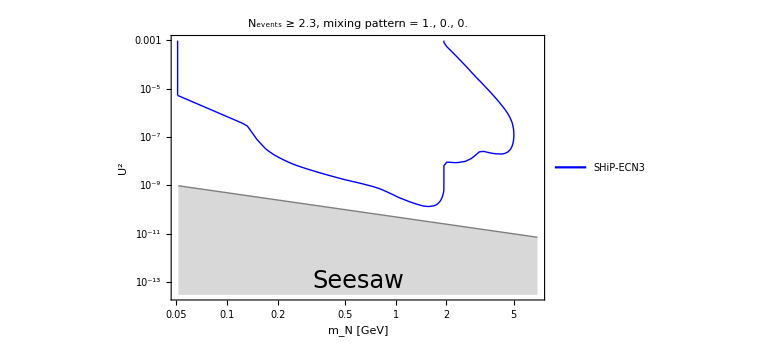

```mathematica
SensitivityBlock[Nev_,Npot_]:=Block[{},
RegSens=RegionPlot[Npot/NpotDefault NevIntTot[10^mN,10^U2]≥ Nev,{mN,Log10[mNminMaxOverall[[1]]],Log10[mNminMaxOverall[[2]]]},{U2,Log10[U2minmaxOverall[[1]]],Log10[U2minmaxOverall[[2]]]}];
SensTemp=Cases[Normal@RegSens,Line[x_]:>x,Infinity];
Sens=Table[{10^#[[1]],10^#[[2]]}&/@SensTemp[[i]],{i,1,Length[SensTemp],1}];
Export[FileNameJoin[{NotebookDirectory[],"Sensitivity domains","HNLs",ExperimentFolder,ToString@StringForm["Sensitivity_HNL_MixingPattern_``-``-``_type_``_at_``_Nev=``_Npot=``.xls",Sequence@@{SelectedMixingPattern[[1]]//ToString,SelectedMixingPattern[[2]]//ToString,SelectedMixingPattern[[3]]//ToString,SelectedHNLtype,ExperimentFolder,Nev//ToString,Npot//CForm//ToString}]}],Sens];
Sens
]
U2seesaw[mN_]=(5*10^-11)/mN;
Print["The minimal value of N_events for which the sensitivity will be computed:"]
NevMinVal=DialogInput[{nev=""},Column[{"Enter the value of N_events for which the sensitivity will be computed:",InputField[Dynamic[nev],Number],Button["Proceed",DialogReturn[nev],ImageSize->Automatic]}]]//N
choiceNPoT=dropdownDialog[{"Yes","No"},Row[{"The number of proton collisions is ", NpotDefault,". Would you like to change it?"}]]
If[choiceNPoT=="Yes",NpotSelected=DialogInput[{br=""},Column[{"Enter the number of proton collisions",InputField[Dynamic[br],String],Button["Proceed",DialogReturn[br],ImageSize->Automatic]}]]//ToExpression//N,NpotSelected=NpotDefault]
sens=SensitivityBlock[NevMinVal,NpotSelected];
Show[ListLogLogPlot[Cases[{sens,Table[{mN,U2seesaw[mN]},{mN,1.01mNminMaxOverall[[1]],1.1mNminMaxOverall[[2]],(1.1mNminMaxOverall[[2]]-1.01mNminMaxOverall[[1]])/50}]},_?MatrixQ,All],Joined->{True,True,True,True}, Frame-> True,FrameLabel->{"m_N [GeV]" , "U^2"},FrameStyle->Directive[Black, 23],PlotStyle->Flatten[{ConstantArray[{Thick,Blue},If[MatrixQ[sens],1,Length@sens]],ConstantArray[{Thick,Gray},1]},1],Filling->{Length[sens]+1->{Bottom,Directive[Gray,Opacity[0.3]]}},
ImageSize->Large,PlotRange->{{1.01mNminMaxOverall[[1]],1.1mNminMaxOverall[[2]]},{0.3U2minmaxOverall[[1]],0.99U2minmaxOverall[[2]]}},PlotLabel->Style[Row[{"N_events ≥ ",NevMinVal,", mixing pattern = ",SelectedMixingPattern[[1]],", ",SelectedMixingPattern[[2]],", ",SelectedMixingPattern[[3]]}],18,Black],PlotLegends->Placed[Style[#,15]&/@{ExperimentFolder},{0.2,0.15}]],Graphics[{Text[Style["Seesaw",24,Black],Scaled[{0.5,0.07}]]}]]
SensitivityBlock[2.3];
```